# Integration Rules for ∫(sin^j(z))^m(a+b sin^k(z))^n ⅆz when j^2=1∧k^2=1

Domain Map

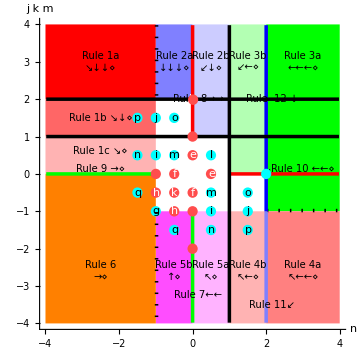

Legend:
•  The rule number in a colored region indicates the rule to use for integrals in that region.
•  The rule number next to a colored line indicates the rule to use for integrals on that line.
•  A white region or line indicates there is no rule for integrals in that region or on that line.
•  A solid black line indicates integrals on that line are handled by rules in another section.
•  A dashed black line on the border of a region indicates integrals on that border are handled by the rule for that region.
•  The arrow(s) following a rule number indicates the direction the rule drives integrands in the n×m exponent plane.
•  A ⋄ following a rule number indicates the rule transforms the integrand into a form handled by another section.
•  A red (stop) disk indicates the terminal rule to use for the point at the center of the disk.
•  A cyan disk indicates the non-terminal rule to use for the point at the center of the disk.

# Integration Rules for ∫(sin^j(z))^m ⅆz when j^2=1

Rule a:  ∫Sin[c+d x]^j ⅆx

#### Reference: G&R 2.01.5, CRC 290, A&S 4.3.113

#### Derivation: Rule 8b with m=1 and j=1

#### Note: This rule is an unnecessary special case of rule 8b, but it saves a step.

#### Rule a1:

∫Sin[c+d x]ⅆx  ⟶  -Cos[c+d x]/d

#### Program code:

```mathematica
Int[sin[c_.+d_.*x_],x_Symbol] :=
  -Cos[c+d*x]/d /;
FreeQ[{c,d},x]
```

#### Reference: G&R 2.01.6, CRC 291, A&S 4.3.114

```mathematica
Int[Cos[a_.+b_.*x_],x_Symbol] :=
  Sin[a+b*x]/b /;
FreeQ[{a,b},x]
```

#### Reference: G&R 2.526.1, CRC 295, A&S 4.3.116'

#### Derivation: Integration by substitution

#### Basis: Csc[z]=-1/(1-Cos[z]^2)Cos'[z]

#### Rule a2:

∫Csc[c+d x]ⅆx  ⟶  -ArcTanh[Cos[c+d x]]/d

#### Program code:

```mathematica
Int[1/sin[c_.+d_.*x_],x_Symbol] :=
  -ArcTanh[Cos[c+d*x]]/d /;
FreeQ[{c,d},x]
```

#### Reference: G&R 2.526.9', CRC 294', A&S 4.3.117'

```mathematica
Int[Sec[a_.+b_.*x_],x_Symbol] :=
  ArcTanh[Sin[a+b*x]]/b /;
FreeQ[{a,b},x]
```

Rule b:  ∫Sin[c+d x]^(2j)ⅆx

#### Reference: G&R 2.513.5, CRC 296

#### Derivation: Rule 8b with m=2 and j=1

#### Note: This rule is an unnecessary special case of rule 8b, but it saves a step.

#### Rule b1:

∫Sin[c+d x]^2 ⅆx  ⟶  x/2-(Cos[c+d x] Sin[c+d x])/(2 d)

#### Program code:

```mathematica
Int[sin[c_.+d_.*x_]^2,x_Symbol] :=
  x/2 - Cos[c+d*x]*Sin[c+d*x]/(2*d) /;
FreeQ[{c,d},x]
```

#### Reference: G&R 2.513.11, CRC 302

```mathematica
Int[Cos[a_.+b_.*x_]^2,x_Symbol] :=
  x/2 + Cos[a+b*x]*Sin[a+b*x]/(2*b) /;
FreeQ[{a,b},x]
```

#### Reference: G&R 2.526.2, CRC 308

#### Derivation: Rule 7b with m=-2 and j=1

#### Note: This rule is an unnecessary special case of rule 7b, but it saves a step.

#### Rule b2:

∫Csc[c+d x]^2 ⅆx  ⟶  -Cot[c+d x]/d

#### Program code:

```mathematica
Int[1/sin[c_.+d_.*x_]^2,x_Symbol] :=
  -Cot[c+d*x]/d /;
FreeQ[{c,d},x]
```

#### Reference: G&R 2.526.10, CRC 312

```mathematica
Int[Sec[a_.+b_.*x_]^2,x_Symbol] :=
  Tan[a+b*x]/b /;
FreeQ[{a,b},x]
```

Rules 7-8:  ∫(Sin[c+d x]^j)^m ⅆx

#### Derivation: Integration by substitution

#### Basis: If m/2∈ℤ, then Csc[z]^m=-(1+Cot[z]^2)^((m-2)/2) Cot'[z]

#### Note: This rule is used for odd m<-2 since it requires fewer steps and results in simpler antiderivatives than rule 7b.

#### Rule 7a: If m/2∈ℤ ∧ m<-2, then

∫Sin[c+d x]^m ⅆx  ⟶  -1/dSubst[∫(1+x^2)^((-m-2)/2)ⅆx,x,Cot[c+d x]]

#### Program code:

```mathematica
Int[sin[c_.+d_.*x_]^m_,x_Symbol] :=
  Dist[-1/d,Subst[Int[Expand[(1+x^2)^((-m-2)/2),x],x],x,Cot[c+d*x]]] /;
FreeQ[{c,d},x] && EvenQ[m] && m<-2
```

```mathematica
Int[Sec[a_.+b_.*x_]^n_,x_Symbol] :=
  Dist[1/b,Subst[Int[Regularize[(1+x^2)^((n-2)/2),x],x],x,Tan[a+b*x]]] /;
FreeQ[{a,b},x] && EvenQ[n] && n>2
```

#### Reference: G&R 2.510.3, CRC 309

#### Reference: G&R 2.552.3 special case when a=0

#### Derivation: Rule 5b with a=1, b=0, k=j and n=0

#### Rule 7b: If j^2=1 ∧ m/2∉ℤ ∧ m<-1, then

∫(Sin[c+d x]^j)^m ⅆx  ⟶  (2Cos[c+d x](Sin[c+d x]^j)^(m+1))/(d(2m+j+1))+(2 m+j+3)/(2 m+j+1)∫(Sin[c+d x]^j)^(m+2)ⅆx

#### Program code:

```mathematica
Int[(sin[c_.+d_.*x_]^j_.)^m_,x_Symbol] :=
  2*Cos[c+d*x]*(Sin[c+d*x]^j)^(m+1)/(d*(2*m+j+1)) + 
  Dist[(2*m+j+3)/(2*m+j+1),Int[(sin[c+d*x]^j)^(m+2),x]] /;
FreeQ[{c,d},x] && OneQ[j^2] && Not[EvenQ[m]] && RationalQ[m] && m<-1
```

#### Reference: G&R 2.510.6, CRC 313

```mathematica
Int[Cos[a_.+b_.*x_]^n_,x_Symbol] :=
  -Sin[a+b*x]*Cos[a+b*x]^(n+1)/(b*(n+1)) +
  Dist[(n+2)/(n+1),Int[Cos[a+b*x]^(n+2),x]] /;
FreeQ[{a,b},x] && RationalQ[n] && n<-1
```

```mathematica
Int[Sec[a_.+b_.*x_]^n_,x_Symbol] :=
  Sin[a+b*x]*Sec[a+b*x]^(n-1)/(b*(n-1)) + 
  Dist[(n-2)/(n-1),Int[Sec[a+b*x]^(n-2),x]] /;
FreeQ[{a,b},x] && RationalQ[n] && n>1
```

#### Derivation: Integration by substitution

#### Basis: If (m-1)/2∈ℤ, then Sin[z]^m=-(1-Cos[z]^2)^((m-1)/2) Cos'[z]

#### Note: This rule is used for odd m>1 since it requires fewer steps and results in simpler antiderivatives than rule 8b.

#### Rule 8a: If (m-1)/2∈ℤ ∧ m>1, then

∫Sin[c+d x]^m ⅆx  ⟶  -1/dSubst[∫(1-x^2)^((m-1)/2)ⅆx,x,Cos[c+d x]]

#### Program code:

```mathematica
Int[sin[c_.+d_.*x_]^m_,x_Symbol] :=
  Dist[-1/d,Subst[Int[Expand[(1-x^2)^((m-1)/2),x],x],x,Cos[c+d*x]]] /;
FreeQ[{c,d},x] && OddQ[m] && m>1
```

```mathematica
Int[Cos[a_.+b_.*x_]^n_,x_Symbol] :=
  Dist[1/b,Subst[Int[Expand[(1-x^2)^((n-1)/2),x],x],x,Sin[a+b*x]]] /;
FreeQ[{a,b},x] && OddQ[n] && n>1
```

#### Reference: G&R 2.510.2, CRC 299

#### Reference: G&R 2.552.3 inverted special case when a=0

#### Derivation: Rule 2b with k=j and n=0

#### Rule 8b: If j^2=1 ∧ (m-1)/2∉ℤ ∧ m>1, then

∫(Sin[c+d x]^j)^m ⅆx  ⟶  -(2Cos[c+d x](Sin[c+d x]^j)^(m-1))/(d (2m+j-1))+(2m+j-3)/(2m+j-1) ∫(Sin[c+d x]^j)^(m-2)ⅆx

#### Program code:

```mathematica
Int[(sin[c_.+d_.*x_]^j_.)^m_,x_Symbol] :=
  -2*Cos[c+d*x]*(Sin[c+d*x]^j)^(m-1)/(d*(2*m+j-1)) + 
  Dist[(2*m+j-3)/(2*m+j-1),Int[(sin[c+d*x]^j)^(m-2),x]] /;
FreeQ[{c,d},x] && OneQ[j^2] && Not[OddQ[m]] && RationalQ[m] && m>1
```

#### Reference: G&R 2.510.5, CRC 305

```mathematica
Int[Cos[a_.+b_.*x_]^n_,x_Symbol] :=
  Sin[a+b*x]*Cos[a+b*x]^(n-1)/(b*n) +
  Dist[(n-1)/n,Int[Cos[a+b*x]^(n-2),x]] /;
FreeQ[{a,b},x] && RationalQ[n] && n>1
```

```mathematica
Int[Sec[a_.+b_.*x_]^n_,x_Symbol] :=
  -Sin[a+b*x]*Sec[a+b*x]^(n+1)/(b*n) + 
  Dist[(n+1)/n,Int[Sec[a+b*x]^(n+2),x]] /;
FreeQ[{a,b},x] && RationalQ[n] && n<-1
```

# Integration Rules for ∫(a+b sin^k(z))^n ⅆz when k^2=1

Rule c:  ∫1/(a+b Sin[c+d x]^k)ⅆx

#### Note: Although this rule produces a slightly more complicated antiderivative than rule c2 and c4, it is continuous provided a^2-b^2>0.

#### Rule c1: If a^2-b^2>0, then

∫1/(a+b Sin[c+d x])ⅆx  ⟶  x/(√(a^2-b^2))+2/(d √(a^2-b^2))ArcTan[(b Cos[c+d x])/(a+√(a^2-b^2)+b Sin[c+d x])]

#### Program code:

```mathematica
Int[1/(a_+b_.*sin[c_.+d_.*x_]),x_Symbol] :=
  x/Rt[a^2-b^2,2] + 
  2/(d*Rt[a^2-b^2,2])*ArcTan[Sim[b*Cos[c+d*x]/(a+Rt[a^2-b^2,2]+b*Sin[c + d*x])]] /;
FreeQ[{a,b,c,d},x] && PositiveQ[a^2-b^2]
```

```mathematica
Int[1/(a_+b_.*Cos[c_.+d_.*x_]),x_Symbol] :=
  x/Rt[a^2-b^2,2] - 2/(d*Rt[a^2-b^2,2])*ArcTan[Sim[b*Sin[c+d*x]/(a+Rt[a^2-b^2,2]+b*Cos[c + d*x])]] /;
FreeQ[{a,b,c,d},x] && PositiveQ[a^2-b^2]
```

#### Reference: G&R 2.553.3a, A&S 4.3.133a

#### Note: Although nonessential, this rule produces a slightly simpler antiderivative than rule c3.

#### Rule c2: If a^2-b^2>0, then

∫1/(a+b Cos[c+d x])ⅆx  ⟶  2/(d √(a^2-b^2))ArcTan[((a-b) Tan[1/2 (c+d x)])/(√(a^2-b^2))]

#### Program code:

```mathematica
Int[1/(a_+b_.*sin[c_.+Pi/2+d_.*x_]),x_Symbol] :=
  2*ArcTan[(a-b)*Tan[(c+d*x)/2]/Rt[a^2-b^2,2]]/(d*Rt[a^2-b^2,2]) /;
FreeQ[{a,b,c,d},x] && PosQ[a^2-b^2]
```

#### Reference: G&R 2.551.3a, A&S 4.3.131a

#### Rule c3: If a^2-b^2>0, then

∫1/(a+b Sin[c+d x])ⅆx  ⟶  2/(d √(a^2-b^2))ArcTan[(b+a Tan[1/2 (c+d x)])/(√(a^2-b^2))]

#### Program code:

```mathematica
Int[1/(a_+b_.*sin[c_.+d_.*x_]),x_Symbol] :=
  2*ArcTan[(b+a*Tan[(c+d*x)/2])/Rt[a^2-b^2,2]]/(d*Rt[a^2-b^2,2]) /;
FreeQ[{a,b,c,d},x] && PosQ[a^2-b^2]
```

#### Reference: G&R 2.553.3b', A&S 4.3.133b'

#### Note: Although nonessential, this rule produces a slightly simpler antiderivative than rule c5.

#### Rule c4: If ¬(a^2-b^2>0), then

∫1/(a+b Cos[c+d x])ⅆx  ⟶  -2/(d √(b^2-a^2))ArcTanh[((a-b) Tan[1/2 (c+d x)])/(√(b^2-a^2))]

#### Program code:

```mathematica
Int[1/(a_+b_.*sin[c_.+Pi/2+d_.*x_]),x_Symbol] :=
  -2*ArcTanh[(a-b)*Tan[(c+d*x)/2]/Rt[b^2-a^2,2]]/(d*Rt[b^2-a^2,2]) /;
FreeQ[{a,b,c,d},x] && NegQ[a^2-b^2]
```

#### Reference: G&R 2.551.3b', A&S 4.3.131b'

#### Rule c5: If ¬(a^2-b^2>0), then

∫1/(a+b Sin[c+d x])ⅆx  ⟶  -2/(d √(b^2-a^2))ArcTanh[(b+a Tan[1/2 (c+d x)])/(√(b^2-a^2))]

#### Program code:

```mathematica
Int[1/(a_+b_.*sin[c_.+d_.*x_]),x_Symbol] :=
  -2*ArcTanh[(b+a*Tan[(c+d*x)/2])/Rt[b^2-a^2,2]]/(d*Rt[b^2-a^2,2]) /;
FreeQ[{a,b,c,d},x] && NegQ[a^2-b^2]
```

#### Derivation: Algebraic expansion

#### Basis: 1/(a+b/z)=1/a-b/(a(b+a z))

#### Rule c6: If a^2-b^2≠0, then

∫1/(a+b Csc[c+d x])ⅆx  ⟶  x/a-b/a∫1/(b+a Sin[c+d x])ⅆx

#### Program code:

```mathematica
Int[1/(a_+b_.*sin[c_.+d_.*x_]^(-1)),x_Symbol] :=
  x/a - Dist[b/a,Int[1/(b+a*sin[c+d*x]),x]] /;
FreeQ[{a,b,c,d},x] && NonzeroQ[a^2-b^2]
```

Rule d: ∫(a+b Sin[c+d x]^k)^2 ⅆx

#### Derivation: Rule 12 with m=0

#### Rule d: If k^2=1, then

∫(a+b Sin[c+d x]^k)^2 ⅆx  ⟶  (a^2+(k+1)/(k+3)b^2)x-(2 b^2 Cos[c+d x]Sin[c+d x]^k)/(d (k+3))+2a b∫Sin[c+d x]^k ⅆx

#### Program code:

```mathematica
Int[(a_+b_.*sin[c_.+d_.*x_]^k_.)^2,x_Symbol] :=
  (a^2+(k+1)/(k+3)*b^2)*x - 2*b^2*Cos[c+d*x]*Sin[c+d*x]^k/(d*(k+3)) + 2*a*b*Int[sin[c+d*x]^k,x] /;
FreeQ[{a,b,c,d},x] && OneQ[k^2]
```

Rule e: ∫√(a+b Sin[c+d x])ⅆx

#### Basis: ∂_z EllipticE[z,n]=√(1-n Sin[z]^2)

#### Basis: 1-(2 b)/(a+b)Sin[(c+d x)/2-π/4]^2=a/(a+b)+(b Sin[c+d x])/(a+b)

#### Rule e1: If a^2-b^2≠0 ∧ a+b>0, then

∫√(a+b Sin[c+d x])ⅆx  ⟶  -(2 √(a+b))/dEllipticE[π/4-(c+d x)/2,(2 b)/(a+b)]

#### Program code:

```mathematica
Int[Sqrt[a_.+b_.*sin[c_.+Pi/2+d_.*x_]],x_Symbol] :=
  2*Sqrt[Sim[a+b]]/d*EllipticE[(c+d*x)/2,Sim[2*b/(a+b)]] /;
FreeQ[{a,b,c,d},x] && NonzeroQ[a^2-b^2] && PositiveQ[a+b]
```

```mathematica
Int[Sqrt[a_.+b_.*sin[c_.+d_.*x_]],x_Symbol] :=
  -2*Sqrt[Sim[a+b]]/d*EllipticE[Pi/4-(c+d*x)/2,Sim[2*b/(a+b)]] /;
FreeQ[{a,b,c,d},x] && NonzeroQ[a^2-b^2] && PositiveQ[a+b]
```

#### Derivation: Piecewise constant extraction

#### Basis: ∂_z (√(a/(a+b)+b/(a+b)f[z]))/(√(a+b f[z]))=0

#### Note: Since a/(a+b)+b/(a+b)=1>0, rule e1 applies to the resulting integrand.

#### Rule e2: If a^2-b^2≠0 ∧ ¬(a+b>0), then

∫√(a+b Sin[c+d x])ⅆx  ⟶  ((a+b)√(a/(a+b)+b/(a+b)Sin[c+d x]))/(√(a+b Sin[c+d x]))∫√(a/(a+b)+b/(a+b)Sin[c+d x])ⅆx

#### Program code:

```mathematica
Int[Sqrt[a_.+b_.*sin[c_.+d_.*x_]],x_Symbol] :=
  (a+b)*Sqrt[(a+b*Sin[c+d*x])/(a+b)]/Sqrt[a+b*Sin[c+d*x]]*Int[Sqrt[a/(a+b)+b/(a+b)*sin[c+d*x]],x] /;
FreeQ[{a,b,c,d},x] && NonzeroQ[a^2-b^2] && Not[PositiveQ[a+b]]
```

Rule f: ∫1/(√(a+b Sin[c+d x]))ⅆx

#### Basis: ∂_x EllipticF[x,n]=1/(√(1-n Sin[x]^2))

#### Basis: 1-(2 b)/(a+b)Sin[(c+d x)/2-π/4]^2=a/(a+b)+(b Sin[c+d x])/(a+b)

#### Rule f1: If a^2-b^2≠0 ∧ a+b>0, then

∫1/(√(a+b Sin[c+d x]))ⅆx  ⟶  -2/(d √(a+b))EllipticF[π/4-(c+d x)/2,(2 b)/(a+b)]

#### Program code:

```mathematica
Int[1/Sqrt[a_.+b_.*sin[c_.+Pi/2+d_.*x_]],x_Symbol] :=
  2/(d*Sqrt[Sim[a+b]])*EllipticF[(c+d*x)/2,Sim[2*b/(a+b)]] /;
FreeQ[{a,b,c,d},x] && NonzeroQ[a^2-b^2] && PositiveQ[a+b]
```

```mathematica
Int[1/Sqrt[a_.+b_.*sin[c_.+d_.*x_]],x_Symbol] :=
  -2/(d*Sqrt[Sim[a+b]])*EllipticF[Pi/4-(c+d*x)/2,Sim[2*b/(a+b)]] /;
FreeQ[{a,b,c,d},x] && NonzeroQ[a^2-b^2] && PositiveQ[a+b]
```

#### Derivation: Piecewise constant extraction

#### Basis: ∂_z (√((a+b f[z])/(a+b)))/(√(a+b f[z]))=0

#### Note: Since a/(a+b)+b/(a+b)=1>0, rule f1 applies to the resulting integrand.

#### Rule f2: If a^2-b^2≠0 ∧ ¬(a+b>0), then

∫1/(√(a+b Sin[c+d x]))ⅆx  ⟶  (√(a/(a+b)+b/(a+b)Sin[c+d x]))/(√(a+b Sin[c+d x]))∫1/(√(a/(a+b)+b/(a+b)Sin[c+d x]))ⅆx

#### Program code:

```mathematica
Int[1/Sqrt[a_.+b_.*sin[c_.+d_.*x_]],x_Symbol] :=
  Sqrt[(a+b*Sin[c+d*x])/(a+b)]/Sqrt[a+b*Sin[c+d*x]]*Int[1/Sqrt[a/(a+b)+b/(a+b)*sin[c+d*x]],x] /;
FreeQ[{a,b,c,d},x] && NonzeroQ[a^2-b^2] && Not[PositiveQ[a+b]]
```

∫(a+b Csc[c+d x])^(n/2)ⅆx

#### Derivation: Piecewise constant extraction

#### Basis: ∂_z (f[z]^(n/2)(b/f[z])^(n/2))=0

#### Rule: If n^2=1, then

∫(b Csc[c+d x])^(n/2)ⅆx  ⟶  (Sin[c+d x])^(n/2)(b Csc[c+d x])^(n/2)∫1/Sin[c+d x]^(n/2)ⅆx

#### Program code:

```mathematica
Int[(b_.*sin[c_.+d_.*x_]^(-1))^n_,x_Symbol] :=
  Dist[Sin[c+d*x]^n*(b*Csc[c+d*x])^n,Int[1/sin[c+d*x]^n,x]] /;
FreeQ[{b,c,d},x] && ZeroQ[n^2-1/4]
```

#### Derivation: Piecewise constant extraction

#### Basis: ∂_z (√(b+a f[z]))/(√f[z]√(a+b/f[z]))=0

#### Rule: If a^2-b^2≠0 ∧ n-1/2∈ℤ ∧ -2<n<2, then

∫(a+b Csc[c+d x])^n ⅆx  ⟶  (√(b+a Sin[c+d x]))/(√Sin[c+d x]√(a+b Csc[c+d x]))∫(b+a Sin[c+d x])^n/Sin[c+d x]^n ⅆx

#### Program code:

```mathematica
Int[(a_+b_.*sin[c_.+d_.*x_]^(-1))^n_,x_Symbol] :=
  Dist[Sqrt[b+a*Sin[c+d*x]]/(Sqrt[Sin[c+d*x]]*Sqrt[a+b*Csc[c+d*x]]),
    Int[(b+a*sin[c+d*x])^n/sin[c+d*x]^n,x]] /;
FreeQ[{a,b,c,d},x] && NonzeroQ[a^2-b^2] && IntegerQ[n-1/2] && -2<n<2
```

Rules 17-18:  ∫(a+b Csc[c+d x])^n ⅆx

#### Derivation: Rule 6 with m=0 and k=-1

#### Rule 17: If a^2-b^2≠0 ∧ n<-1, then

∫(a+b Csc[c+d x])^n ⅆx  ⟶  
(b^2 Cot[c+d x](a+b Csc[c+d x])^(n+1))/(a d (n+1) (a^2-b^2))+1/(a (n+1) (a^2-b^2))·
∫((a^2-b^2) (n+1)-a b(n+1)Csc[c+d x]+b^2(n+2)Csc[c+d x]^2)(a+b Csc[c+d x])^(n+1)ⅆx

#### Program code:

```mathematica
Int[(a_+b_.*sin[c_.+d_.*x_]^(-1))^n_,x_Symbol] :=
  b^2*Cot[c+d*x]*(a+b*Csc[c+d*x])^(n+1)/(a*d*(n+1)*(a^2-b^2)) + 
  Dist[1/(a*(n+1)*(a^2-b^2)),
    Int[((a^2-b^2)*(n+1)-(a*b*(n+1))*sin[c+d*x]^(-1)+(b^2*(n+2))*sin[c+d*x]^(-2))*
      (a+b*sin[c+d*x]^(-1))^(n+1),x]] /;
FreeQ[{a,b,c,d},x] && NonzeroQ[a^2-b^2] && RationalQ[n] && n<-1
```

#### Derivation: Rule 3a with m=0 and k=-1

#### Rule 18: If a^2-b^2≠0 ∧ n>2, then

∫(a+b Csc[c+d x])^n ⅆx  ⟶  
-(b^2 Cot[c+d x](a+b Csc[c+d x])^(n-2))/(d(n-1))+1/(n-1) ·
∫(a^3(n-1)+b(b^2(n-2)+3 a^2(n-1))Csc[c+d x]+a b^2(3n-4)Csc[c+d x]^2)(a+b Csc[c+d x])^(n-3)ⅆx

#### Program code:

```mathematica
Int[(a_+b_.*sin[c_.+d_.*x_]^(-1))^n_,x_Symbol] :=
  -b^2*Cot[c+d*x]*(a+b*Csc[c+d*x])^(n-2)/(d*(n-1)) + 
  Dist[1/(n-1),
    Int[(a^3*(n-1)+(b*(b^2*(n-2)+3*a^2*(n-1)))*sin[c+d*x]^(-1)+(a*b^2*(3*n-4))*sin[c+d*x]^(-2))*
      (a+b*sin[c+d*x]^(-1))^(n-3),x]] /;
FreeQ[{a,b,c,d},x] && NonzeroQ[a^2-b^2] && RationalQ[n] && n>2
```

Rules 15-16:  ∫(b Sin[c+d x]^k)^n ⅆx

#### Derivation: Rule 10a inverted

#### Rule 15: If k^2=1 ∧ n<-1, then

∫(b Sin[c+d x]^k)^n ⅆx  ⟶  (2Cos[c+d x](b Sin[c+d x]^k)^(n+1))/(b d (2n+k+1))+(2n+k+3)/(b^2(2n+k+1))∫(b Sin[c+d x]^k)^(n+2)ⅆx

#### Program code:

```mathematica
Int[(b_.*sin[c_.+d_.*x_]^k_.)^n_,x_Symbol] :=
  2*Cos[c+d*x]*(b*Sin[c+d*x]^k)^(n+1)/(b*d*(2*n+k+1)) + 
  Dist[(2*n+k+3)/(b^2*(2*n+k+1)),Int[(b*sin[c+d*x]^k)^(n+2),x]] /;
FreeQ[{b,c,d},x] && OneQ[k^2] && RationalQ[n] && n<-1
```

#### Derivation: Rule 3a or 3b with m=0 and a=0

#### Rule 16: If k^2=1 ∧ n>1, then

∫(b Sin[c+d x]^k)^n ⅆx  ⟶  -(2b Cos[c+d x](b Sin[c+d x]^k)^(n-1))/(d (2n+k-1))+(b^2 (2 n+k-3))/(2 n+k-1) ∫(b Sin[c+d x]^k)^(n-2)ⅆx

#### Program code:

```mathematica
Int[(b_.*sin[c_.+d_.*x_]^k_.)^n_,x_Symbol] :=
  -2*b*Cos[c+d*x]*(b*Sin[c+d*x]^k)^(n-1)/(d*(2*n+k-1)) + 
  Dist[b^2*(2*n+k-3)/(2*n+k-1),Int[(b*sin[c+d*x]^k)^(n-2),x]] /;
FreeQ[{b,c,d},x] && OneQ[k^2] && RationalQ[n] && n>1
```

# Integration Rules for ∫(sin^j(z))^m(a+b sin^k(z))^n ⅆz when j^2=1∧k^2=1

Rule g:  ∫1/(Sin[c+d x](a+b Sin[c+d x]))ⅆx

#### Derivation: Algebraic expansion

#### Basis: 1/(z(a+b z))=1/(a z)-b/(a(a+b z))

#### Rule g:

∫1/(Sin[c+d x](a+b Sin[c+d x]))ⅆx  ⟶  1/a∫1/Sin[c+d x]ⅆx-b/a∫1/(a+b Sin[c+d x])ⅆx

#### Program code:

```mathematica
Int[1/(sin[c_.+d_.*x_]*(a_.+b_.*sin[c_.+d_.*x_])),x_Symbol] :=
  1/a*Int[1/Sin[c+d*x],x] - b/a*Int[1/(a+b*Sin[c+d*x]),x] /;
FreeQ[{a,b,c,d},x]
```

```mathematica
Int[1/((a_.+b_.*sin[c_.+d_.*x_])*(e_+f_.*sin[c_.+d_.*x_])),x_Symbol] :=
  b/(b*e-a*f)*Int[1/(a+b*sin[c+d*x]),x] - 
  f/(b*e-a*f)*Int[1/(e+f*sin[c+d*x]),x] /;
FreeQ[{a,b,c,d,e,f},x] && NonzeroQ[b*e-a*f]
```

Rule h:  ∫1/((a+b Sin[c+d x])√(e+f Sin[c+dx]))ⅆx

#### Basis: ∂_z EllipticPi[2m,z/2-π/4,2n]=1/(2 (1-m+m Sin[z]) √(1-n+n Sin[z]))

#### Rule h1: If a^2-b^2≠0 ∧ e^2-f^2≠0 ∧ e+f>0, then

∫1/((a+b Sin[c+d x])√(e+f Sin[c+dx]))ⅆx  ⟶  2/(d(a+b)√(e+f))EllipticPi[(2 b)/(a+b),(c+d x)/2-π/4,(2 f)/(e+f)]

#### Program code:

```mathematica
Int[1/((a_.+b_.*sin[c_.+Pi/2+d_.*x_])*Sqrt[e_.+f_.*sin[c_.+Pi/2+d_.*x_]]),x_Symbol] :=
  2/(d*(a+b)*Rt[e+f,2])*EllipticPi[Sim[2*b/(a+b)],(c+d*x)/2,Sim[2*f/(e+f)]] /;
FreeQ[{a,b,c,d,e,f},x] && NonzeroQ[a^2-b^2] && NonzeroQ[e^2-f^2] && PositiveQ[e+f]
```

```mathematica
Int[1/((a_.+b_.*sin[c_.+d_.*x_])*Sqrt[e_.+f_.*sin[c_.+d_.*x_]]),x_Symbol] :=
  2/(d*(a+b)*Rt[e+f,2])*EllipticPi[Sim[2*b/(a+b)],(c+d*x)/2-Pi/4,Sim[2*f/(e+f)]] /;
FreeQ[{a,b,c,d,e,f},x] && NonzeroQ[a^2-b^2] && NonzeroQ[e^2-f^2] && PositiveQ[e+f]
```

#### Derivation: Piecewise constant extraction

#### Basis: ∂_z (√((e+f g[z])/(e+f)))/(√(e+f g[z]))=0

#### Note: Since e/(e+f)+f/(e+f)=1>0, rule h1 applies to the resulting integrand.

#### Rule h2: If a^2-b^2≠0 ∧ e^2-f^2≠0 ∧ ¬(e+f>0), then

∫1/((a+b Sin[c+d x])√(e+f Sin[c+dx]))ⅆx  ⟶  
(√((e+f Sin[c+d x])/(e+f)))/(√(e+f Sin[c+d x]))∫1/((a+b Sin[c+d x])√(e/(e+f)+f/(e+f)Sin[c+d x]))ⅆx

#### Program code:

```mathematica
Int[1/((a_.+b_.*sin[c_.+d_.*x_])*Sqrt[e_.+f_.*sin[c_.+d_.*x_]]),x_Symbol] :=
  Sqrt[(e+f*Sin[c+d*x])/(e+f)]/Sqrt[e+f*Sin[c+d*x]]*
    Int[1/((a+b*sin[c+d*x])*Sqrt[e/(e+f)+f/(e+f)*sin[c+d*x]]),x] /;
FreeQ[{a,b,c,d},x] && NonzeroQ[a^2-b^2] && NonzeroQ[e^2-f^2] && Not[PositiveQ[e+f]]
```

Rule i:  ∫(√(a+b Sin[c+d x]))/(e+f Sin[c+d x])ⅆx

#### Derivation: Algebraic expansion

#### Basis: (√(a+b z))/(e+f z)=b/(f √(a+b z))+(a f-b e)/(f(e+f z)√(a +b z))

#### Rule i: If a^2-b^2≠0 ∧ e^2-f^2≠0 ∧ a f-b e≠0, then

∫(√(a+b Sin[c+d x]))/(e+f Sin[c+d x])ⅆx  ⟶  
b/f∫1/(√(a+b Sin[c+d x]))ⅆx+(a f-b e)/f∫1/((e+f Sin[c+d x])√(a+b Sin[c+d x]))ⅆx

#### Program code:

```mathematica
Int[Sqrt[a_.+b_.*sin[c_.+d_.*x_]]/(e_.+f_.*sin[c_.+d_.*x_]),x_Symbol] :=
  b/f*Int[1/Sqrt[a+b*sin[c+d*x]],x] + 
  (a*f-b*e)/f*Int[1/((e+f*sin[c+d*x])*Sqrt[a+b*sin[c+d*x]]),x] /;
FreeQ[{a,b,c,d,e,f},x] && NonzeroQ[a^2-b^2] && NonzeroQ[e^2-f^2] && NonzeroQ[a*f-b*e]
```

Rule j:  ∫(a+b Sin[c+d x])^(3/2)/(e+f Sin[c+d x])ⅆx

#### Derivation: Algebraic expansion

#### Basis: (a+b z)^(3/2)/(e+f z)=(b √(a+b z))/f+((a f-b e)√(a +b z))/(f(e+f z))

#### Rule j: If a^2-b^2≠0 ∧ e^2-f^2≠0 ∧ a f-b e≠0, then

∫(a+b Sin[c+d x])^(3/2)/(e+f Sin[c+d x])ⅆx  ⟶  b/f∫√(a+b Sin[c+d x])ⅆx+(a f-b e)/f∫(√(a+b Sin[c+d x]))/(e+f Sin[c+d x])ⅆx

#### Program code:

```mathematica
Int[(a_.+b_.*sin[c_.+d_.*x_])^(3/2)/(e_.+f_.*sin[c_.+d_.*x_]),x_Symbol] :=
  b/f*Int[Sqrt[a+b*sin[c+d*x]],x] + 
  Dist[(a*f-b*e)/f,Int[Sqrt[a+b*sin[c+d*x]]/(e+f*sin[c+d*x]),x]] /;
FreeQ[{a,b,c,d,e,f},x] && NonzeroQ[a^2-b^2] && NonzeroQ[e^2-f^2] && NonzeroQ[a*f-b*e]
```

Rule k:  ∫1/(√Sin[c+dx]√(a+b Sin[c+dx]))ⅆx

#### Derivation: Algebraic expansion

#### Basis: If b>0 ∧ b-a>0, then √(a+b z)=√(1+z) √((a+b z)/(1+z))

#### Rule k1: If b>0 ∧ b^2-a^2>0, then

∫1/(√Sin[c+d x]√(a+b Sin[c+d x]))ⅆx  ⟶  2/(d √(a+b))EllipticF[ArcSin[Tan[(c+d x)/2-π/4]],-(a-b)/(a+b)]

#### Program code:

```mathematica
Int[1/(Sqrt[sin[c_.+d_.*x_]]*Sqrt[a_+b_.*sin[c_.+d_.*x_]]),x_Symbol] :=
  2/(d*Sqrt[a+b])*EllipticF[ArcSin[Tan[(c-Pi/2+d*x)/2]],-Sim[(a-b)/(a+b)]] /;
FreeQ[{a,b,c,d},x] && PositiveQ[b] && PositiveQ[b^2-a^2]
```

#### Derivation: Piecewise constant extraction

#### Basis: ∂_z ((√(1+f[z]))/(√(a+b f[z]))√((a+b f[z])/((a+b) (1+f[z]))))=0

#### Rule k2: If a^2-b^2≠0, then

∫1/(√Sin[c+d x] √(a+b Sin[c+d x]))  ⟶  
(2 √(1+Sin[c+d x]))/(d √(a+b Sin[c+d x]))√((a+b Sin[c+d x])/((a+b) (1+Sin[c+d x])))EllipticF[ArcSin[Tan[(c+d x)/2-π/4]],-(a-b)/(a+b)]

#### Program code:

```mathematica
Int[1/(Sqrt[sin[c_.+d_.*x_]]*Sqrt[a_+b_.*sin[c_.+d_.*x_]]),x_Symbol] :=
  2*Sqrt[1+Sin[c+d*x]]/(d*Sqrt[a+b*Sin[c+d*x]])*
  Sqrt[(a+b*Sin[c+d*x])/((a+b)*(1+Sin[c+d*x]))]*
  EllipticF[ArcSin[Tan[(c-Pi/2+d*x)/2]],-Sim[(a-b)/(a+b)]] /;
FreeQ[{a,b,c,d},x] && NonzeroQ[a^2-b^2]
```

Rule l:  ∫√Sin[c+d x] √(a+b Sin[c+d x])ⅆx

#### Derivation: Algebraic expansion

#### Rule l: If a^2-b^2≠0, then

∫√Sin[c+d x] √(a+b Sin[c+d x])ⅆx  ⟶  
-a∫1/(√Sin[c+d x] √(a+b Sin[c+d x]))ⅆx+∫(a+a Sin[c+d x]+b Sin[c+d x]^2)/(√Sin[c+d x] √(a+b Sin[c+d x]))ⅆx

#### Program code:

```mathematica
Int[Sqrt[sin[c_.+d_.*x_]]*Sqrt[a_+b_.*sin[c_.+d_.*x_]],x_Symbol] :=
  -a*Int[1/(Sqrt[sin[c+d*x]]*Sqrt[a+b*sin[c+d*x]]),x] + 
  Int[(a+a*sin[c+d*x]+b*sin[c+d*x]^2)/(Sqrt[sin[c+d*x]]*Sqrt[a+b*sin[c+d*x]]),x] /;
FreeQ[{a,b,c,d},x] && NonzeroQ[a^2-b^2]
```

Rule m:  ∫(√(a+b Sin[c+d x]))/(√(e+f Sin[c+d x]))ⅆx

#### Derivation: Algebraic expansion

#### Rule m1: If a^2-b^2≠0, then

∫(√Sin[c+d x])/(√(a+b Sin[c+d x]))ⅆx  ⟶  
-∫1/(√Sin[c+d x]√(a+b Sin[c+d x]))ⅆx+∫(1+Sin[c+d x])/(√Sin[c+d x]√(a+b Sin[c+d x]))ⅆx

#### Program code:

```mathematica
Int[Sqrt[sin[c_.+d_.*x_]]/Sqrt[a_+b_.*sin[c_.+d_.*x_]],x_Symbol] :=
  -Int[1/(Sqrt[sin[c+d*x]]*Sqrt[a+b*sin[c+d*x]]),x] +
  Int[(1+sin[c+d*x])/(Sqrt[sin[c+d*x]]*Sqrt[a+b*sin[c+d*x]]),x] /;
FreeQ[{a,b,c,d},x] && NonzeroQ[a^2-b^2]
```

#### Derivation: Algebraic expansion

#### Rule m2: If a^2-b^2≠0, then

∫(√(a+b Sin[c+d x]))/(√Sin[c+d x])ⅆx  ⟶  
(a-b)∫1/(√Sin[c+d x]√(a+b Sin[c+d x]))ⅆx+b∫(1+Sin[c+d x])/(√Sin[c+d x]√(a+b Sin[c+d x]))ⅆx

#### Program code:

```mathematica
Int[Sqrt[a_+b_.*sin[c_.+d_.*x_]]/Sqrt[sin[c_.+d_.*x_]],x_Symbol] :=
  (a-b)*Int[1/(Sqrt[sin[c+d*x]]*Sqrt[a+b*sin[c+d*x]]),x] +
  Dist[b,Int[(1+sin[c+d*x])/(Sqrt[sin[c+d*x]]*Sqrt[a+b*sin[c+d*x]]),x]] /;
FreeQ[{a,b,c,d},x] && NonzeroQ[a^2-b^2]
```

#### Derivation: Algebraic expansion

#### Note: This rule unifies rules m1 and m2, but requires messy application conditions.

#### Rule: If a^2-b^2≠0 ∧ e^2-f^2≠0 ∧ b e-a f≠0, then

∫(√(a+b Sin[c+d x]))/(√(e+f Sin[c+d x]))ⅆx  ⟶  
(a-b)∫1/(√(a+b Sin[c+d x])√(e+f Sin[c+d x]))ⅆx+b∫(1+Sin[c+d x])/(√(a+b Sin[c+d x])√(e+f Sin[c+d x]))ⅆx

#### Program code:

```mathematica
(* Int[Sqrt[a_.+b_.*sin[c_.+d_.*x_]]/Sqrt[e_.+f_.*sin[c_.+d_.*x_]],x_Symbol] :=
  (a-b)*Int[1/(Sqrt[a+b*sin[c+d*x]]*Sqrt[e+f*sin[c+d*x]]),x] +
  Dist[b,Int[(1+sin[c+d*x])/(Sqrt[a+b*sin[c+d*x]]*Sqrt[e+f*sin[c+d*x]]),x]] /;
FreeQ[{a,b,c,d,e,f},x] && NonzeroQ[a^2-b^2] && NonzeroQ[e^2-f^2] && NonzeroQ[b*e-a*f] *)
```

Rule n:  ∫(√(a+b Sin[c+d x]))/(e+f Sin[c+d x])^(3/2)ⅆx

#### Derivation: Algebraic expansion

#### Rule n1: If a^2-b^2≠0, then

∫(√Sin[c+d x])/(a+b Sin[c+d x])^(3/2)ⅆx  ⟶  
-1/(a-b)∫1/(√Sin[c+d x]√(a+b Sin[c+d x]))ⅆx+a/(a-b)∫(1+Sin[c+d x])/(√Sin[c+d x](a+b Sin[c+d x])^(3/2))ⅆx

#### Program code:

```mathematica
Int[Sqrt[sin[c_.+d_.*x_]]/(a_+b_.*sin[c_.+d_.*x_])^(3/2),x_Symbol] :=
  -1/(a-b)*Int[1/(Sqrt[sin[c+d*x]]*Sqrt[a+b*sin[c+d*x]]),x] + 
  Dist[a/(a-b),Int[(1+sin[c+d*x])/(Sqrt[sin[c+d*x]]*(a+b*sin[c+d*x])^(3/2)),x]] /; 
FreeQ[{a,b,c,d},x] && NonzeroQ[a^2-b^2]
```

#### Derivation: Algebraic expansion

#### Rule n2: If a^2-b^2≠0, then

∫(√(a+b Sin[c+d x]))/Sin[c+d x]^(3/2)ⅆx  ⟶  
(a+b)∫1/(√Sin[c+d x]√(a+b Sin[c+d x]))ⅆx+a∫(1-Sin[c+d x])/(Sin[c+d x]^(3/2)√(a+b Sin[c+d x]))ⅆx

#### Program code:

```mathematica
Int[Sqrt[a_+b_.*sin[c_.+d_.*x_]]/sin[c_.+d_.*x_]^(3/2),x_Symbol] :=
  Dist[a+b,Int[1/(Sqrt[sin[c+d*x]]*Sqrt[a+b*sin[c+d*x]]),x]] + 
  Dist[a,Int[(1-sin[c+d*x])/(sin[c+d*x]^(3/2)*Sqrt[a+b*sin[c+d*x]]),x]] /; 
FreeQ[{a,b,c,d},x] && NonzeroQ[a^2-b^2]
```

#### Derivation: Algebraic expansion

#### Note: This rule unifies rules n1 and n2, but requires messy application conditions.

#### Rule: If a^2-b^2≠0 ∧ e^2-f^2≠0 ∧ b e-a f≠0, then

∫(√(a+b Sin[c+d x]))/(e+f Sin[c+d x])^(3/2)ⅆx  ⟶  
(a-b)/(e-f)∫1/(√(a+b Sin[c+d x])√(e+f Sin[c+d x]))ⅆx+(b e-a f)/(e-f)∫(1+Sin[c+d x])/(√(a+b Sin[c+d x])(e+f Sin[c+d x])^(3/2))ⅆx

#### Program code:

```mathematica
(* Int[Sqrt[a_.+b_.*sin[c_.+d_.*x_]]/(e_.+f_.*sin[c_.+d_.*x_])^(3/2),x_Symbol] :=
  Dist[(a-b)/(e-f),Int[1/(Sqrt[a+b*sin[c+d*x]]*Sqrt[e+f*sin[c+d*x]]),x]] + 
  Dist[(b*e-a*f)/(e-f),Int[(1+sin[c+d*x])/(Sqrt[a+b*sin[c+d*x]]*(e+f*sin[c+d*x])^(3/2)),x]] /; 
FreeQ[{a,b,c,d,e,f},x] && NonzeroQ[a^2-b^2] && NonzeroQ[e^2-f^2] && NonzeroQ[b*e-a*f] *)
```

Rule o:  ∫(a+b Sin[c+d x])^(3/2)/(√(e+f Sin[c+d x]))ⅆx

#### Derivation: Algebraic expansion

#### Rule o1: If a^2-b^2≠0, then

∫Sin[c+d x]^(3/2)/(√(a+b Sin[c+d x]))ⅆx  ⟶  
-a/(2 b)∫(1+Sin[c+d x])/(√Sin[c+d x] √(a+b Sin[c+d x]))ⅆx+1/(2b)∫(a+a Sin[c+d x]+2 b Sin[c+d x]^2)/(√Sin[c+d x] √(a+b Sin[c+d x]))ⅆx

#### Program code:

```mathematica
Int[sin[c_.+d_.*x_]^(3/2)/Sqrt[a_+b_.*sin[c_.+d_.*x_]],x_Symbol] :=
  -a/(2*b)*Int[(1+sin[c+d*x])/(Sqrt[sin[c+d*x]]*Sqrt[a+b*sin[c+d*x]]),x] + 
  Dist[1/(2*b),
    Int[(a+a*sin[c+d*x]+2*b*sin[c+d*x]^2)/(Sqrt[sin[c+d*x]]*Sqrt[a+b*sin[c+d*x]]),x]] /;
FreeQ[{a,b,c,d},x] && NonzeroQ[a^2-b^2]
```

#### Derivation: Algebraic expansion

#### Rule o2: If a^2-b^2≠0, then

∫(a+b Sin[c+d x])^(3/2)/(√Sin[c+d x])ⅆx  ⟶  
(3a b)/2∫(1+Sin[c+d x])/(√Sin[c+d x] √(a+b Sin[c+d x]))ⅆx+1/2∫(a (2 a-3 b)+a b Sin[c+d x]+2 b^2 Sin[c+d x]^2)/(√Sin[c+d x] √(a+b Sin[c+d x]))ⅆx

#### Program code:

```mathematica
Int[(a_+b_.*sin[c_.+d_.*x_])^(3/2)/Sqrt[sin[c_.+d_.*x_]],x_Symbol] :=
  3*a*b/2*Int[(1+sin[c+d*x])/(Sqrt[sin[c+d*x]]*Sqrt[a+b*sin[c+d*x]]),x] + 
  Dist[1/2,
    Int[(a*(2*a-3*b)+a*b*sin[c+d*x]+2*b^2*sin[c+d*x]^2)/(Sqrt[sin[c+d*x]]*Sqrt[a+b*sin[c+d*x]]),x]] /;
FreeQ[{a,b,c,d},x] && NonzeroQ[a^2-b^2]
```

Rule p:  ∫(a+b Sin[c+d x])^(3/2)/(e+f Sin[c+d x])^(3/2)ⅆx

#### Derivation: Algebraic expansion

#### Rule p1: If a^2-b^2≠0, then

∫Sin[c+d x]^(3/2)/(a+b Sin[c+d x])^(3/2)ⅆx  ⟶  1/b∫(1+Sin[c+d x])/(√Sin[c+d x]√(a+b Sin[c+d x]))ⅆx+1/b∫(-a-(a+b) Sin[c+d x])/(√Sin[c+d x](a+b Sin[c+d x])^(3/2))ⅆx

#### Program code:

```mathematica
Int[sin[c_.+d_.*x_]^(3/2)/(a_+b_.*sin[c_.+d_.*x_])^(3/2),x_Symbol] :=
  1/b*Int[(1+sin[c+d*x])/(Sqrt[sin[c+d*x]]*Sqrt[a+b*sin[c+d*x]]),x] + 
  Dist[1/b,Int[(-a-(a+b)*sin[c+d*x])/(Sqrt[sin[c+d*x]]*(a+b*sin[c+d*x])^(3/2)),x]] /;
FreeQ[{a,b,c,d},x] && NonzeroQ[a^2-b^2]
```

#### Derivation: Algebraic expansion

#### Rule p2: If a^2-b^2≠0, then

∫(a+b Sin[c+d x])^(3/2)/Sin[c+d x]^(3/2)ⅆx  ⟶  b^2∫(1+Sin[c+d x])/(√Sin[c+d x]√(a+b Sin[c+d x]))ⅆx+∫(a^2+b(2 a-b) Sin[c+d x])/((Sin[c+d x])^(3/2)√(a+b Sin[c+d x]))ⅆx

#### Program code:

```mathematica
Int[(a_+b_.*sin[c_.+d_.*x_])^(3/2)/sin[c_.+d_.*x_]^(3/2),x_Symbol] :=
  b^2*Int[(1+sin[c+d*x])/(Sqrt[sin[c+d*x]]*Sqrt[a+b*sin[c+d*x]]),x] + 
  Int[(a^2+b*(2*a-b)*sin[c+d*x])/(sin[c+d*x]^(3/2)*Sqrt[a+b*sin[c+d*x]]),x] /;
FreeQ[{a,b,c,d},x] && NonzeroQ[a^2-b^2]
```

#### Derivation: Algebraic expansion

#### Note: This rule unifies rules p1 and p2, but requires messy application conditions.

#### Rule: If a^2-b^2≠0 ∧ e^2-f^2≠0 ∧ b e-a f≠0, then

∫(a+b Sin[c+d x])^(3/2)/(e+f Sin[c+d x])^(3/2)ⅆx  ⟶  b^2/f∫(1+Sin[c+d x])/(√(a+b Sin[c+d x])√(e+f Sin[c+d x]))ⅆx+1/f∫(a^2 f-b^2 e+b (2 a f-b (e+f)) Sin[c+d x])/(√(a+b Sin[c+d x])(e+f Sin[c+d x])^(3/2))ⅆx

#### Program code:

```mathematica
(* Int[(a_.+b_.*sin[c_.+d_.*x_])^(3/2)/(e_.+f_.*sin[c_.+d_.*x_])^(3/2),x_Symbol] :=
  b^2/f*Int[(1+sin[c+d*x])/(Sqrt[a+b*sin[c+d*x]]*Sqrt[e+f*sin[c+d*x]]),x] + 
  Dist[1/f,
    Int[(a^2*f-b^2*e+b*(2*a*f-b*(e+f))*sin[c+d*x])/(Sqrt[a+b*sin[c+d*x]]*(e+f*sin[c+d*x])^(3/2)),x]] /;
FreeQ[{a,b,c,d,e,f},x] && NonzeroQ[a^2-b^2] && NonzeroQ[e^2-f^2] && NonzeroQ[b*e-a*f] *)
```

Rule q:  ∫1/(√(a+b Sin[c+d x]) (e+f Sin[c+d x])^(3/2))ⅆx

#### Derivation: Algebraic expansion

#### Rule q1: If a^2-b^2≠0, then

∫1/(√Sin[c+d x] (a+b Sin[c+d x])^(3/2))ⅆx  ⟶  
1/(a-b)∫1/(√Sin[c+d x] √(a+b Sin[c+d x]))ⅆx-b/(a-b)∫(1+Sin[c+d x])/(√Sin[c+d x] (a+b Sin[c+d x])^(3/2))ⅆx

#### Program code:

```mathematica
Int[1/(Sqrt[sin[c_.+d_.*x_]]*(a_+b_.*sin[c_.+d_.*x_])^(3/2)),x_Symbol] :=
  1/(a-b)*Int[1/(Sqrt[sin[c+d*x]]*Sqrt[a+b*sin[c+d*x]]),x] - 
  Dist[b/(a-b),Int[(1+sin[c+d*x])/(Sqrt[sin[c+d*x]]*(a+b*sin[c+d*x])^(3/2)),x]] /;
FreeQ[{a,b,c,d},x] && NonzeroQ[a^2-b^2]
```

#### Derivation: Algebraic expansion

#### Rule q2: If a^2-b^2≠0, then

∫1/(Sin[c+d x]^(3/2) √(a+b Sin[c+d x]))ⅆx  ⟶  
∫1/(√Sin[c+d x] √(a+b Sin[c+d x]))ⅆx+∫(1-Sin[c+d x])/(Sin[c+d x]^(3/2) √(a+b Sin[c+d x]))ⅆx

#### Program code:

```mathematica
Int[1/(sin[c_.+d_.*x_]^(3/2)*Sqrt[a_+b_.*sin[c_.+d_.*x_]]),x_Symbol] :=
  Int[1/(Sqrt[sin[c+d*x]]*Sqrt[a+b*sin[c+d*x]]),x] + 
  Int[(1-sin[c+d*x])/(sin[c+d*x]^(3/2)*Sqrt[a+b*sin[c+d*x]]),x] /;
FreeQ[{a,b,c,d},x] && NonzeroQ[a^2-b^2]
```

∫(√(a+b Sin[c+d x]))/(√Sin[c+d x] (A+A Sin[c+d x]))ⅆx

#### Basis: If b>0 ∧ b-a>0, then √(a+b z)=√(1+z) √((a+b z)/(1+z))

#### Rule: If b>0 ∧ b^2-a^2>0, then

∫(√(a+b Sin[c+d x]))/(√Sin[c+d x] (A+A Sin[c+d x]))ⅆx  ⟶  (√(a+b))/(d A)EllipticE[ArcSin[Tan[(c+d x)/2-π/4]],-(a-b)/(a+b)]

#### Program code:

```mathematica
Int[Sqrt[a_+b_.*sin[c_.+d_.*x_]]/(Sqrt[sin[c_.+d_.*x_]]*(A_+B_.*sin[c_.+d_.*x_])),x_Symbol] :=
  Sqrt[a+b]/(d*A)*EllipticE[ArcSin[Tan[(c-Pi/2+d*x)/2]],-Sim[(a-b)/(a+b)]] /;
FreeQ[{a,b,c,d,A,B},x] && ZeroQ[A-B] && PositiveQ[b] && PositiveQ[b^2-a^2]
```

#### Derivation: Piecewise constant extraction

#### Basis: ∂_z ((√(1+f[z]))/(√(a+b f[z]))√((a+b f[z])/((a+b) (1+f[z]))))=0

#### Rule: If a^2-b^2≠0, then

∫(√(a+b Sin[c+d x]))/(√Sin[c+d x] (A+A Sin[c+d x]))  ⟶  
((a+b)√(1+ Sin[c+d x]))/(d A √(a+b Sin[c+d x]))√((a+b Sin[c+d x])/((a+b) (1+Sin[c+d x])))EllipticE[ArcSin[Tan[(c+d x)/2-π/4]],-(a-b)/(a+b)]

#### Program code:

```mathematica
Int[Sqrt[a_+b_.*sin[c_.+d_.*x_]]/(Sqrt[sin[c_.+d_.*x_]]*(A_+B_.*sin[c_.+d_.*x_])),x_Symbol] :=
  (a+b)*Sqrt[1+Sin[c+d*x]]/(d*A*Sqrt[a+b*Sin[c+d*x]])*Sqrt[(a+b*Sin[c+d*x])/((a+b)*(1+Sin[c+d*x]))]*
  EllipticE[ArcSin[Tan[(c-Pi/2+d*x)/2]],-Sim[(a-b)/(a+b)]] /;
FreeQ[{a,b,c,d,A,B},x] && ZeroQ[A-B] && NonzeroQ[a^2-b^2]
```

∫(√Sin[c+d x])/(√(a+b Sin[c+d x]) (A+A Sin[c+d x]))ⅆx

#### Derivation: Algebraic expansion

#### Basis: (√z)/(√(a+b z)(1+z))=a/((a-b)√z √(a+b z))-(√(a+b z))/((a-b)√z (1+z))

#### Rule: If a^2-b^2≠0, then

∫(√Sin[c+d x])/(√(a+b Sin[c+d x]) (A+A Sin[c+d x]))ⅆx  ⟶  
a/(A(a-b))∫1/(√Sin[c+d x] √(a+b Sin[c+d x]))ⅆx-1/(a-b)∫(√(a+b Sin[c+d x]))/(√Sin[c+d x] (A+A Sin[c+d x]))ⅆx

#### Program code:

```mathematica
Int[Sqrt[sin[c_.+d_.*x_]]/(Sqrt[a_.+b_.*sin[c_.+d_.*x_]]*(A_+B_.*sin[c_.+d_.*x_])),x_Symbol] :=
  a/(A*(a-b))*Int[1/(Sqrt[sin[c+d*x]]*Sqrt[a+b*sin[c+d*x]]),x] - 
  1/(a-b)*Int[Sqrt[a+b*sin[c+d*x]]/(Sqrt[sin[c+d*x]]*(A+B*sin[c+d*x])),x] /;
FreeQ[{a,b,c,d,A,B},x] && ZeroQ[A-B] && NonzeroQ[a^2-b^2]
```

∫(A+A Sin[c+d x])/(√Sin[c+d x] √(a+b Sin[c+d x]))ⅆx

#### Derivation: Algebraic expansion

#### Basis: If b>0 ∧ b-a>0, then √(a+b z)=√(1+z) √((a+b z)/(1+z))

#### Rule: If b>0 ∧ b^2-a^2>0, then

∫(A+A Sin[c+d x])/(√Sin[c+d x] √(a+b Sin[c+d x]))ⅆx  ⟶  (4A)/(d √(a+b))EllipticPi[-1,ArcSin[Tan[(c+d x)/2-π/4]],-(a-b)/(a+b)]

#### Program code:

```mathematica
Int[(A_+B_.*sin[c_.+d_.*x_])/(Sqrt[sin[c_.+d_.*x_]]*Sqrt[a_+b_.*sin[c_.+d_.*x_]]),x_Symbol] :=
  4*A/(d*Sqrt[a+b])*EllipticPi[-1,ArcSin[Tan[(c-Pi/2+d*x)/2]],-Sim[(a-b)/(a+b)]] /;
FreeQ[{a,b,c,d,A,B},x] && ZeroQ[A-B] && PositiveQ[b] && PositiveQ[b^2-a^2]
```

#### Derivation: Piecewise constant extraction

#### Basis: ∂_z ((√(1+f[z]))/(√(a+b f[z]))√((a+b f[z])/((a+b) (1+f[z]))))=0

#### Rule: If a^2-b^2≠0, then

∫(A+A Sin[c+d x])/(√Sin[c+d x] √(a+b Sin[c+d x]))  ⟶  
(4A √(1+Sin[c+d x]))/(d √(a+b Sin[c+d x]))√((a+b Sin[c+d x])/((a+b) (1+Sin[c+d x])))EllipticPi[-1,ArcSin[Tan[(c+d x)/2-π/4]],-(a-b)/(a+b)]

#### Program code:

```mathematica
Int[(A_+B_.*sin[c_.+d_.*x_])/(Sqrt[sin[c_.+d_.*x_]]*Sqrt[a_+b_.*sin[c_.+d_.*x_]]),x_Symbol] :=
  4*A*Sqrt[1+Sin[c+d*x]]/(d*Sqrt[a+b*Sin[c+d*x]])*
  Sqrt[(a+b*Sin[c+d*x])/((a+b)*(1+Sin[c+d*x]))]*
  EllipticPi[-1,ArcSin[Tan[(c-Pi/2+d*x)/2]],-Sim[(a-b)/(a+b)]] /;
FreeQ[{a,b,c,d,A,B},x] && ZeroQ[A-B] && NonzeroQ[a^2-b^2]
```

Rule r:  ∫(Sin[c+d x]^j)^m(b Sin[c+d x]^k)^n ⅆx

#### Derivation: Algebraic simplification

#### Rule r1: If k^2=1 ∧ m∈ℤ, then

∫Sin[c+d x]^m(b Sin[c+d x]^k)^n ⅆx  ⟶  1/b^(k m)∫(b Sin[c+d x]^k)^(k m+n)ⅆx

#### Program code:

```mathematica
Int[sin[c_.+d_.*x_]^m_.*(b_.*sin[c_.+d_.*x_]^k_.)^n_.,x_Symbol] :=
  Dist[1/b^(k*m),Int[(b*sin[c+d*x]^k)^(k*m+n),x]] /;
FreeQ[{b,c,d,n},x] && OneQ[k^2] && IntegerQ[m]
```

#### Derivation: Piecewise constant extraction

#### Basis: If j^2=1, then ∂_z (√(b f[z]^k))/((√(f[z]^j))^(j k))=0

#### Rule r2: If j^2=k^2=1 ∧ m-1/2∈ℤ ∧ n-1/2∈ℤ ∧ n>0, then

∫(Sin[c+d x]^j)^m(b Sin[c+d x]^k)^n ⅆx  ⟶  (b^(n-1/2)√(b Sin[c+d x]^k))/((√(Sin[c+d x]^j))^(j k))∫Sin[c+d x]^(j m+k n)ⅆx

#### Program code:

```mathematica
Int[(sin[c_.+d_.*x_]^j_.)^m_*(b_*sin[c_.+d_.*x_]^k_.)^n_,x_Symbol] :=
  Dist[b^(n-1/2)*Sqrt[b*Sin[c+d*x]^k]/(Sqrt[Sin[c+d*x]^j])^(j*k),Int[sin[c+d*x]^(j*m+k*n),x]] /;
FreeQ[{b,c,d},x] && OneQ[j^2,k^2] && IntegerQ[m-1/2] && IntegerQ[n-1/2] && n>0
```

#### Derivation: Piecewise constant extraction

#### Basis: If j^2=1, then ∂_z ((√(f[z]^j))^(j k))/(√(b f[z]^k))=0

#### Rule r3: If j^2=k^2=1 ∧ m-1/2∈ℤ ∧ n-1/2∈ℤ ∧ n<0, then

∫(Sin[c+d x]^j)^m(b Sin[c+d x]^k)^n ⅆx  ⟶  (b^(n+1/2)(√(Sin[c+d x]^j))^(j k))/(√(b Sin[c+d x]^k))∫Sin[c+d x]^(j m+k n)ⅆx

#### Program code:

```mathematica
Int[(sin[c_.+d_.*x_]^j_.)^m_*(b_*sin[c_.+d_.*x_]^k_.)^n_,x_Symbol] :=
  Dist[b^(n+1/2)*(Sqrt[Sin[c+d*x]^j])^(j*k)/Sqrt[b*Sin[c+d*x]^k],Int[sin[c+d*x]^(j*m+k*n),x]] /;
FreeQ[{b,c,d},x] && OneQ[j^2,k^2] && IntegerQ[m-1/2] && IntegerQ[n-1/2] && n<0
```

Rule s:  ∫(Sin[c+d x]^j)^m(a+b Csc[c+d x])^n ⅆx

#### Derivation: Algebraic simplification

#### Rule s1: If j^2=1 ∧ a^2-b^2≠0 ∧ -1/2≤m+j≤3/2, then

∫((Sin[c+d x]^j)^m)/(a+b Csc[c+d x])ⅆx  ⟶  ∫((Sin[c+d x]^j)^(m+j))/(b+a Sin[c+d x])ⅆx

#### Program code:

```mathematica
Int[(sin[c_.+d_.*x_]^j_.)^m_./(a_+b_.*sin[c_.+d_.*x_]^(-1)),x_Symbol] :=
  Int[(sin[c+d*x]^j)^(m+j)/(b+a*sin[c+d*x]),x] /;
FreeQ[{a,b,c,d},x] && OneQ[j^2] && NonzeroQ[a^2-b^2] && RationalQ[m] && -1/2≤m+j≤3/2
```

#### Derivation: Piecewise constant extraction

#### Basis: ∂_z (√(b+a f[z]))/(√f[z]√(a+b/f[z]))=0

#### Rule s2: If a^2-b^2≠0 ∧ m∈ℤ ∧ n-1/2∈ℤ ∧ ((m=1 ∧ -1<n<2) ∨ (m=-1 ∧ -2<n<1) ∨ (m=-2 ∧ -2<n<0)), then

∫Sin[c+d x]^m(a+b Csc[c+d x])^n ⅆx  ⟶  
(√(b+a Sin[c+d x]))/(√Sin[c+d x]√(a+b Csc[c+d x]))∫Sin[c+d x]^(m-n)(b+a Sin[c+d x])^n ⅆx

#### Program code:

```mathematica
Int[sin[c_.+d_.*x_]^m_.*(a_+b_.*sin[c_.+d_.*x_]^(-1))^n_,x_Symbol] :=
  Dist[Sqrt[b+a*Sin[c+d*x]]/(Sqrt[Sin[c+d*x]]*Sqrt[a+b*Csc[c+d*x]]),
    Int[sin[c+d*x]^(m-n)*(b+a*sin[c+d*x])^n,x]] /;
FreeQ[{a,b,c,d},x] && NonzeroQ[a^2-b^2] && IntegerQ[m] && IntegerQ[n-1/2] && 
  (m==1 && -1<n<2 || m==-1 && -2<n<1  || m==-2 && -2<n<0)
```

#### Derivation: Piecewise constant extraction

#### Basis: If j^2=1, then ∂_z (√(b+a f[z]))/((√(f[z]^j))^j √(a+b/f[z]))=0

#### Rule s3: If j^2=1 ∧ a^2-b^2≠0 ∧ m-1/2∈ℤ ∧ n-1/2∈ℤ ∧ -1≤j m-n≤1, then

∫(Sin[c+d x]^j)^m(a+b Csc[c+d x])^n ⅆx  ⟶  
(√(b+a Sin[c+d x]))/((√(Sin[c+d x]^j))^j √(a+b Csc[c+d x]))∫Sin[c+d x]^(j m-n)(b+a Sin[c+d x])^n ⅆx

#### Program code:

```mathematica
Int[(sin[c_.+d_.*x_]^j_.)^m_*(a_+b_.*sin[c_.+d_.*x_]^(-1))^n_,x_Symbol] :=
  Dist[Sqrt[b+a*Sin[c+d*x]]/((Sqrt[Sin[c+d*x]^j])^j*Sqrt[a+b*Csc[c+d*x]]),
    Int[sin[c+d*x]^(j*m-n)*(b+a*sin[c+d*x])^n,x]] /;
FreeQ[{a,b,c,d},x] && OneQ[j^2] && NonzeroQ[a^2-b^2] && IntegerQ[m-1/2] && IntegerQ[n-1/2] && 
  -1<n<2 && -1≤j*m-n≤1
```

Rule t:  ∫Csc[c+d x]^(m/2)(a+b Sin[c+d x]^k)^n ⅆx

#### Derivation: Piecewise constant extraction

#### Basis: ∂_z (√f[z]√(1/f[z]))=0

#### Rule t: If k^2=1 ∧ a^2-b^2≠0 ∧ m-1/2∈ℤ ∧ -1≤n<1, then

∫Csc[c+d x]^m(a+b Sin[c+d x]^k)^n ⅆx  ⟶  √Csc[c+d x]√Sin[c+d x]∫((a+b Sin[c+d x]^k)^n)/Sin[c+d x]^m ⅆx

#### Program code:

```mathematica
Int[(sin[c_.+d_.*x_]^(-1))^m_*(a_+b_.*sin[c_.+d_.*x_]^k_.)^n_,x_Symbol] :=
  Dist[Sqrt[Csc[c+d*x]]*Sqrt[Sin[c+d*x]],
    Int[(a+b*sin[c+d*x]^k)^n/sin[c+d*x]^m,x]] /;
FreeQ[{a,b,c,d},x] && OneQ[k^2] && NonzeroQ[a^2-b^2] && IntegerQ[m-1/2] && RationalQ[n] && 
  (k===1 || -1<m<1 && -1≤n<1)
```

Rules 11-12:  ∫(Sin[c+d x]^j)^m(a+b Sin[c+d x]^k)^2 ⅆx

#### Derivation: Rule 4a with n=2

#### Rule 11: If j^2=k^2=1 ∧ j k m+(k+1)/2≠0 ∧ j k m≤-1, then

∫(Sin[c+d x]^j)^m(a+b Sin[c+d x]^k)^2 ⅆx  ⟶  (a^2 Cos[c+d x] (Sin[c+d x]^j)^(m+j k))/(d(j k m+(k+1)/2))+
1/(j k m+(k+1)/2)∫(Sin[c+d x]^j)^(m+j k)(2a b (j k m+(k+1)/2)+(a^2+(a^2+b^2) (j k m+(k+1)/2)) Sin[c+d x]^k)ⅆx

#### Program code:

```mathematica
Int[(sin[c_.+d_.*x_]^j_.)^m_.*(a_+b_.*sin[c_.+d_.*x_]^k_.)^2,x_Symbol] :=
  a^2*Cos[c+d*x]*(Sin[c+d*x]^j)^(m+j*k)/(d*(j*k*m+(k+1)/2)) + 
  Dist[1/(j*k*m+(k+1)/2),
    Int[(sin[c+d*x]^j)^(m+j*k)*
      Sim[2*a*b*(j*k*m+(k+1)/2)+(a^2+(a^2+b^2)*(j*k*m+(k+1)/2))*sin[c+d*x]^k,x],x]] /;
FreeQ[{a,b,c,d},x] && OneQ[j^2,k^2] && RationalQ[m] && j*k*m+(k+1)/2≠0 && j*k*m≤-1
```

#### Derivation: Rule 3a with n=2

#### Rule 12: If j^2=k^2=1 ∧ j k m+(k+3)/2≠0 ∧ j k m≥-1, then

∫(Sin[c+d x]^j)^m(a+b Sin[c+d x]^k)^2 ⅆx  ⟶  -(b^2 Cos[c+d x](Sin[c+d x]^j)^(m+j k))/(d (j k m+(k+3)/2))+
1/(j k m+(k+3)/2) ∫(Sin[c+d x]^j)^m (a^2+(a^2+b^2)(j k m+(k+1)/2)+2 a b (j k m+(k+3)/2) Sin[c+d x]^k)ⅆx

#### Program code:

```mathematica
Int[(sin[c_.+d_.*x_]^j_.)^m_.*(a_+b_.*sin[c_.+d_.*x_]^k_.)^2,x_Symbol] :=
  -b^2*Cos[c+d*x]*(Sin[c+d*x]^j)^(m+j*k)/(d*(j*k*m+(k+3)/2)) + 
  Dist[1/(j*k*m+(k+3)/2),
    Int[(sin[c+d*x]^j)^m*
      Sim[a^2+(a^2+b^2)*(j*k*m+(k+1)/2)+2*a*b*(j*k*m+(k+3)/2)*sin[c+d*x]^k,x],x]] /;
FreeQ[{a,b,c,d},x] && OneQ[j^2,k^2] && RationalQ[m] && j*k*m+(k+3)/2≠0 && j*k*m≥-1
```

Rules 9-10:  ∫Sin[c+d x]^((k-1)/2)(a+b Sin[c+d x]^k)^n ⅆx

#### Reference: G&R 2.552.3

#### Derivation: Rule 1c with j m=(k-1)/2

#### Rule 9: If k^2=1 ∧ a^2-b^2≠0 ∧ n<-1, then

∫Sin[c+d x]^((k-1)/2)(a+b Sin[c+d x]^k)^n ⅆx  ⟶  -(b Cos[c+d x] Sin[c+d x]^((k-1)/2) (a+b Sin[c+d x]^k)^(n+1))/(d (n+1) (a^2-b^2))+
1/((n+1)(a^2-b^2))∫Sin[c+d x]^((k-1)/2)(a (n+1)-b (n+2) Sin[c+d x]^k)(a+b Sin[c+d x]^k)^(n+1)ⅆx

#### Program code:

```mathematica
Int[(a_+b_.*sin[c_.+d_.*x_])^n_,x_Symbol] :=
  -b*Cos[c+d*x]*(a+b*Sin[c+d*x])^(n+1)/(d*(n+1)*(a^2-b^2)) + 
  Dist[1/((n+1)*(a^2-b^2)),Int[(a*(n+1)-b*(n+2)*sin[c+d*x])*(a+b*sin[c+d*x])^(n+1),x]] /;
FreeQ[{a,b,c,d},x] && NonzeroQ[a^2-b^2] && RationalQ[n] && n<-1
```

```mathematica
Int[sin[c_.+d_.*x_]^(-1)*(a_+b_.*sin[c_.+d_.*x_]^(-1))^n_,x_Symbol] :=
  -b*Cot[c+d*x]*(a+b*Csc[c+d*x])^(n+1)/(d*(n+1)*(a^2-b^2)) + 
  Dist[1/((n+1)*(a^2-b^2)),Int[sin[c+d*x]^(-1)*(a*(n+1)-b*(n+2)*sin[c+d*x]^(-1))*(a+b*sin[c+d*x]^(-1))^(n+1),x]] /;
FreeQ[{a,b,c,d},x] && NonzeroQ[a^2-b^2] && RationalQ[n] && n<-1
```

#### Reference: G&R 2.552.3 inverted

#### Derivation: Rule 3b with j m=(k-1)/2

#### Rule 10: If k^2=1 ∧ a^2-b^2≠0 ∧ n>1, then

∫Sin[c+d x]^((k-1)/2)(a+b Sin[c+d x]^k)^n ⅆx  ⟶  -(b Cos[c+d x]Sin[c+d x]^((k-1)/2)(a+b Sin[c+d x]^k)^(n-1))/(d n)+
1/n ∫(Sin[c+d x])^((k-1)/2) (a^2 n+b^2 (n-1)+a b(2 n-1)Sin[c+d x]^k)(a+b Sin[c+d x]^k)^(n-2)ⅆx

#### Program code:

```mathematica
Int[(a_.+b_.*sin[c_.+d_.*x_])^n_,x_Symbol] :=
  -b*Cos[c+d*x]*(a+b*Sin[c+d*x])^(n-1)/(d*n) + 
  Dist[1/n,Int[Sim[a^2*n+b^2*(n-1)+a*b*(2*n-1)*sin[c+d*x],x]*(a+b*sin[c+d*x])^(n-2),x]] /;
FreeQ[{a,b,c,d},x] && NonzeroQ[a^2-b^2] && RationalQ[n] && n>1
```

```mathematica
Int[sin[c_.+d_.*x_]^(-1)*(a_+b_.*sin[c_.+d_.*x_]^(-1))^n_,x_Symbol] :=
  -b*Cot[c+d*x]*(a+b*Csc[c+d*x])^(n-1)/(d*n) + 
  Dist[1/n,Int[sin[c+d*x]^(-1)*(a^2*n+b^2*(n-1)+a*b*(2*n-1)*sin[c+d*x]^(-1))*(a+b*sin[c+d*x]^(-1))^(n-2),x]] /;
FreeQ[{a,b,c,d},x] && NonzeroQ[a^2-b^2] && RationalQ[n] && n>1
```

Rules 13-14:  ∫Sin[c+d x]^((3k-1)/2)(a+b Sin[c+d x]^k)^n ⅆx

#### Derivation: Rule 1b with j m=(3k-1)/2

#### Rule 13: If k^2=1 ∧ a^2-b^2≠0 ∧ n<-1, then

∫Sin[c+d x]^((3k-1)/2)(a+b Sin[c+d x]^k)^n ⅆx  ⟶  
(a Cos[c+d x] Sin[c+d x]^((k-1)/2) (a+b Sin[c+d x]^k)^(n+1))/(d (n+1) (a^2-b^2))-
1/((n+1)(a^2-b^2))∫Sin[c+d x]^((k-1)/2)(b(n+1)-a(n+2)Sin[c+d x]^k)(a+b Sin[c+d x]^k)^(n+1)ⅆx

#### Program code:

```mathematica
Int[sin[c_.+d_.*x_]^m_*(a_+b_.*sin[c_.+d_.*x_]^k_.)^n_,x_Symbol] :=
  a*Cos[c+d*x]*Sin[c+d*x]^((k-1)/2)*(a+b*Sin[c+d*x]^k)^(n+1)/(d*(n+1)*(a^2-b^2)) - 
  Dist[1/((n+1)*(a^2-b^2)),
    Int[Sin[c+d*x]^((k-1)/2)*(b*(n+1)-a*(n+2)*Sin[c+d*x]^k)*(a+b*Sin[c+d*x]^k)^(n+1),x]] /;
FreeQ[{a,b,c,d},x] && OneQ[k^2] && ZeroQ[m-(3*k-1)/2] && NonzeroQ[a^2-b^2] && RationalQ[n] && n<-1
```

#### Derivation: Algebraic expansion

#### Rule 14a: If k^2=1 ∧ a^2-b^2≠0, then

∫Sin[c+d x]^((3k-1)/2)/(a+b Sin[c+d x]^k)ⅆx  ⟶  1/b∫Sin[c+d x]^((k-1)/2)ⅆx-a/b∫Sin[c+d x]^((k-1)/2)/(a+b Sin[c+d x]^k)ⅆx

#### Program code:

```mathematica
Int[sin[c_.+d_.*x_]^m_/(a_+b_.*sin[c_.+d_.*x_]^k_.),x_Symbol] :=
  1/b*Int[Sin[c+d*x]^((k-1)/2),x] - 
  a/b*Int[Sin[c+d*x]^((k-1)/2)/(a+b*Sin[c+d*x]^k),x] /;
FreeQ[{a,b,c,d},x] && OneQ[k^2] && ZeroQ[m-(3*k-1)/2] && NonzeroQ[a^2-b^2]
```

#### Derivation: Rule 2b with j m=(3k-1)/2

#### Rule 14b: If k^2=1 ∧ n>1, then

∫Sin[c+d x]^((3k-1)/2)(a+b Sin[c+d x]^k)^n ⅆx  ⟶  
-(Cos[c+d x]Sin[c+d x]^((k-1)/2)(a+b Sin[c+d x]^k)^n)/(d (n+1))+
n/(n+1) ∫Sin[c+d x]^((k-1)/2) (b+a Sin[c+d x]^k)(a+b Sin[c+d x]^k)^(n-1)ⅆx

#### Program code:

```mathematica
Int[sin[c_.+d_.*x_]^m_*(a_+b_.*sin[c_.+d_.*x_]^k_.)^n_,x_Symbol] :=
  -Cos[c+d*x]*Sin[c+d*x]^((k-1)/2)*(a+b*Sin[c+d*x]^k)^n/(d*(n+1)) + 
  Dist[n/(n+1),
    Int[Sin[c+d*x]^((k-1)/2)*(b+a*Sin[c+d*x]^k)*(a+b*Sin[c+d*x]^k)^(n-1),x]] /;
FreeQ[{a,b,c,d},x] && OneQ[k^2] && ZeroQ[m-(3*k-1)/2] && RationalQ[n] && n>-1
```

Rules 20-21:  ∫Sin[c+d x]^((5k-1)/2)(a+b Sin[c+d x]^k)^n ⅆx

#### Derivation: Rule 1a with j m=(5k-1)/2

#### Rule 20: If k^2=1 ∧ a^2-b^2≠0 ∧ n<-1, then

∫Sin[c+d x]^((5k-1)/2)(a+b Sin[c+d x]^k)^n ⅆx  ⟶  
-(a^2 Cos[c+d x] Sin[c+d x]^((k-1)/2) (a+b Sin[c+d x]^k)^(n+1))/(b d (n+1) (a^2-b^2))+
1/(b(n+1)(a^2-b^2))∫Sin[c+d x]^((k-1)/2)(a b(n+1)-(a^2+b^2(n+1))Sin[c+d x]^k)(a+b Sin[c+d x]^k)^(n+1)ⅆx

#### Program code:

```mathematica
Int[sin[c_.+d_.*x_]^m_*(a_+b_.*sin[c_.+d_.*x_]^k_.)^n_,x_Symbol] :=
  -a^2*Cos[c+d*x]*Sin[c+d*x]^((k-1)/2)*(a+b*Sin[c+d*x]^k)^(n+1)/(b*d*(n+1)*(a^2-b^2)) + 
  Dist[1/(b*(n+1)*(a^2-b^2)),
    Int[Sin[c+d*x]^((k-1)/2)*(a*b*(n+1)-(a^2+b^2*(n+1))*Sin[c+d*x]^k)*(a+b*Sin[c+d*x]^k)^(n+1),x]] /;
FreeQ[{a,b,c,d},x] && OneQ[k^2] && ZeroQ[m-(5*k-1)/2] && NonzeroQ[a^2-b^2] && RationalQ[n] && n<-1
```

#### Derivation: Rule 21b with n=-1

#### Rule 21a: If k^2=1, then

∫Sin[c+d x]^((5k-1)/2)/(a+b Sin[c+d x]^k)ⅆx  ⟶  -(Cos[c+d x]Sin[c+d x]^((k-1)/2))/(b d)-a/b∫Sin[c+d x]^((3k-1)/2)/(a+b Sin[c+d x]^k)ⅆx

#### Program code:

```mathematica
Int[sin[c_.+d_.*x_]^m_/(a_+b_.*sin[c_.+d_.*x_]^k_.),x_Symbol] :=
  -Cos[c+d*x]*Sin[c+d*x]^((k-1)/2)/(b*d) - 
  Dist[a/b,Int[Sin[c+d*x]^((3*k-1)/2)/(a+b*Sin[c+d*x]^k),x]] /;
FreeQ[{a,b,c,d},x] && OneQ[k^2] && ZeroQ[m-(5*k-1)/2]
```

#### Derivation: Rule 2a with j m=(5k-1)/2

#### Rule 21b: If k^2=1 ∧ n>1, then

∫Sin[c+d x]^((5k-1)/2)(a+b Sin[c+d x]^k)^n ⅆx  ⟶  
-(Cos[c+d x]Sin[c+d x]^((k-1)/2)(a+b Sin[c+d x]^k)^(n+1))/(b d (n+2))+
1/(b (n+2))∫Sin[c+d x]^((k-1)/2) (b(n+1)-a Sin[c+d x]^k)(a+b Sin[c+d x]^k)^n ⅆx

#### Program code:

```mathematica
Int[sin[c_.+d_.*x_]^m_*(a_+b_.*sin[c_.+d_.*x_]^k_.)^n_,x_Symbol] :=
  -Cos[c+d*x]*Sin[c+d*x]^((k-1)/2)*(a+b*Sin[c+d*x]^k)^(n+1)/(b*d*(n+2)) + 
  Dist[1/(b*(n+2)),
    Int[Sin[c+d*x]^((k-1)/2)*(b*(n+1)-a*Sin[c+d*x]^k)*(a+b*Sin[c+d*x]^k)^n,x]] /;
FreeQ[{a,b,c,d},x] && OneQ[k^2] && ZeroQ[m-(5*k-1)/2] && RationalQ[n] && n>-1
```

Rules 1-6:  ∫(Sin[c+d x]^j)^m(a+b Sin[c+d x]^k)^n ⅆx

#### Derivation: Recurrence 1 with A=0, B=0, C=1 and m=m-2

#### Rule 1a: If j^2=k^2=1 ∧ a^2-b^2≠0 ∧ j k m>2 ∧ n<-1, then

∫(Sin[c+d x]^j)^m(a+b Sin[c+d x]^k)^n ⅆx  ⟶  
-(a^2 Cos[c+d x] (Sin[c+d x]^j)^(m-2j k) (a+b Sin[c+d x]^k)^(n+1))/(b d (n+1) (a^2-b^2))+1/(b(n+1)(a^2-b^2))·
∫(Sin[c+d x]^j)^(m-3j k)(a^2(j k m+(k-1)/2-2)+a b(n+1)Sin[c+d x]^k-(b^2(n+1)+a^2(j k m+(k-1)/2-1))Sin[c+d x]^(2k))(a+b Sin[c+d x]^k)^(n+1)ⅆx

#### Program code:

```mathematica
Int[(sin[c_.+d_.*x_]^j_.)^m_.*(a_+b_.*sin[c_.+d_.*x_]^k_.)^n_,x_Symbol] :=
  -a^2*Cos[c+d*x]*(Sin[c+d*x]^j)^(m-2*j*k)*(a+b*Sin[c+d*x]^k)^(n+1)/(b*d*(n+1)*(a^2-b^2)) + 
  Dist[1/(b*(n+1)*(a^2-b^2)),
    Int[(sin[c+d*x]^j)^(m-3*j*k)*
      Sim[a^2*(j*k*m+(k-1)/2-2)+a*b*(n+1)*sin[c+d*x]^k-
        (b^2*(n+1)+a^2*(j*k*m+(k-1)/2-1))*sin[c+d*x]^(2*k),x]*
      (a+b*sin[c+d*x]^k)^(n+1),x]] /;
FreeQ[{a,b,c,d},x] && OneQ[j^2,k^2] && NonzeroQ[a^2-b^2] && RationalQ[m,n] && j*k*m>2 && n<-1
```

#### Derivation: Recurrence 1 with A=0, B=1, C=0 and m=m-1

#### Derivation: Recurrence 6 with A=0, B=0, C=1 and m=m-2

#### Rule 1b: If j^2=k^2=1 ∧ a^2-b^2≠0 ∧ 1<j k m<2 ∧ n<-1, then

∫(Sin[c+d x]^j)^m(a+b Sin[c+d x]^k)^n ⅆx  ⟶  
(a Cos[c+d x] (Sin[c+d x]^j)^(m-j k) (a+b Sin[c+d x]^k)^(n+1))/(d (n+1) (a^2-b^2))-1/((n+1)(a^2-b^2))·
∫(Sin[c+d x]^j)^(m-2j k)(a(j k m+(k-1)/2-1)+b(n+1)Sin[c+d x]^k-a(j k m+n+(k+1)/2)Sin[c+d x]^(2k))(a+b Sin[c+d x]^k)^(n+1)ⅆx

#### Program code:

```mathematica
Int[(sin[c_.+d_.*x_]^j_.)^m_*(a_+b_.*sin[c_.+d_.*x_]^k_.)^n_,x_Symbol] :=
  a*Cos[c+d*x]*(Sin[c+d*x]^j)^(m-j*k)*(a+b*Sin[c+d*x]^k)^(n+1)/(d*(n+1)*(a^2-b^2)) - 
  Dist[1/((n+1)*(a^2-b^2)),
    Int[(sin[c+d*x]^j)^(m-2*j*k)*
      Sim[a*(j*k*m+(k-1)/2-1)+b*(n+1)*sin[c+d*x]^k-a*(j*k*m+n+(k+1)/2)*sin[c+d*x]^(2*k),x]*
      (a+b*sin[c+d*x]^k)^(n+1),x]] /;
FreeQ[{a,b,c,d},x] && OneQ[j^2,k^2] && NonzeroQ[a^2-b^2] && RationalQ[m,n] && 
  1<j*k*m<2 && n<-1
```

#### Derivation: Recurrence 1 with A=1, B=0 and C=0

#### Derivation: Recurrence 6 with A=0, B=1, C=0 and m=m-1

#### Rule 1c: If j^2=k^2=1 ∧ a^2-b^2≠0 ∧ 0<j k m<1 ∧ n<-1, then

∫(Sin[c+d x]^j)^m(a+b Sin[c+d x]^k)^n ⅆx  ⟶  
-(b Cos[c+d x] (Sin[c+d x]^j)^m (a+b Sin[c+d x]^k)^(n+1))/(d (n+1) (a^2-b^2))+1/((n+1)(a^2-b^2))·
∫(Sin[c+d x]^j)^(m-j k)(b(j k m+(k-1)/2)+a(n+1)Sin[c+d x]^k-b(j k m+n+(k+1)/2+1)Sin[c+d x]^(2k))(a+b Sin[c+d x]^k)^(n+1)ⅆx

#### Program code:

```mathematica
Int[(sin[c_.+d_.*x_]^j_.)^m_.*(a_+b_.*sin[c_.+d_.*x_]^k_.)^n_,x_Symbol] :=
  -b*Cos[c+d*x]*(Sin[c+d*x]^j)^m*(a+b*Sin[c+d*x]^k)^(n+1)/(d*(n+1)*(a^2-b^2)) + 
  Dist[1/((n+1)*(a^2-b^2)),
    Int[(sin[c+d*x]^j)^(m-j*k)*
      Sim[b*(j*k*m+(k-1)/2)+a*(n+1)*sin[c+d*x]^k-b*(j*k*m+n+(k+1)/2+1)*sin[c+d*x]^(2*k),x]*
      (a+b*sin[c+d*x]^k)^(n+1),x]] /;
FreeQ[{a,b,c,d},x] && OneQ[j^2,k^2] && NonzeroQ[a^2-b^2] && RationalQ[m,n] && 
  0<j*k*m<1 && n<-1
```

#### Derivation: Recurrence 2 with A=0, B=0, C=1 and m=m-2

#### Rule 2a: If j^2=k^2=1 ∧ a^2-b^2≠0 ∧ j k m>2 ∧ -1≤n<0, then

∫(Sin[c+d x]^j)^m(a+b Sin[c+d x]^k)^n ⅆx  ⟶  
-(Cos[c+d x](Sin[c+d x]^j)^(m-2j k)(a+b Sin[c+d x]^k)^(n+1))/(b d (j k m+n+(k-1)/2))+1/(b (j k m+n+(k-1)/2))·
∫(Sin[c+d x]^j)^(m-3j k) (a(j k m+(k-1)/2-2)+b(j k m+n+(k-1)/2-1)Sin[c+d x]^k-a(j k m+(k-1)/2-1)Sin[c+d x]^(2k))(a+b Sin[c+d x]^k)^n ⅆx

#### Program code:

```mathematica
Int[(sin[c_.+d_.*x_]^j_.)^m_*(a_.+b_.*sin[c_.+d_.*x_]^k_.)^n_,x_Symbol] :=
  -Cos[c+d*x]*(Sin[c+d*x]^j)^(m-2*j*k)*(a+b*Sin[c+d*x]^k)^(n+1)/(b*d*(j*k*m+n+(k-1)/2)) + 
  Dist[1/(b*(j*k*m+n+(k-1)/2)),
    Int[(sin[c+d*x]^j)^(m-3*j*k)*
      Sim[a*(j*k*m+(k-1)/2-2)+b*(j*k*m+n+(k-1)/2-1)*sin[c+d*x]^k-
        a*(j*k*m+(k-1)/2-1)*sin[c+d*x]^(2*k),x]*
      (a+b*sin[c+d*x]^k)^n,x]] /;
FreeQ[{a,b,c,d},x] && OneQ[j^2,k^2] && NonzeroQ[a^2-b^2] && RationalQ[m,n] && j*k*m>2 && -1≤n<0
```

#### Derivation: Recurrence 2 with A=0, B=a, C=b, m=m-1 and n=n-1

#### Derivation: Recurrence 3 with A=0, B=0, C=1 and m=m-2

#### Rule 2b: If j^2=k^2=1 ∧ a^2-b^2≠0 ∧ j k m>1 ∧ j k m≠2 ∧ 0<n<1, then

∫(Sin[c+d x]^j)^m(a+b Sin[c+d x]^k)^n ⅆx  ⟶  
-(Cos[c+d x](Sin[c+d x]^j)^(m-j k)(a+b Sin[c+d x]^k)^n)/(d (j k m+n+(k-1)/2))+1/(j k m+n+(k-1)/2)·
 ∫(Sin[c+d x]^j)^(m-2j k) (a (j k m+(k-1)/2-1)+b(j k m+n+(k-1)/2-1)Sin[c+d x]^k+a n Sin[c+d x]^(2k))(a+b Sin[c+d x]^k)^(n-1)ⅆx

#### Program code:

```mathematica
Int[(sin[c_.+d_.*x_]^j_.)^m_*(a_.+b_.*sin[c_.+d_.*x_]^k_.)^n_,x_Symbol] :=
  -Cos[c+d*x]*(Sin[c+d*x]^j)^(m-j*k)*(a+b*Sin[c+d*x]^k)^n/(d*(j*k*m+n+(k-1)/2)) + 
  Dist[1/(j*k*m+n+(k-1)/2),
    Int[(sin[c+d*x]^j)^(m-2*j*k)*
      Sim[a*(j*k*m+(k-1)/2-1)+b*(j*k*m+n+(k-1)/2-1)*sin[c+d*x]^k+a*n*sin[c+d*x]^(2*k),x]*
      (a+b*sin[c+d*x]^k)^(n-1),x]] /;
FreeQ[{a,b,c,d},x] && OneQ[j^2,k^2] && NonzeroQ[a^2-b^2] && RationalQ[m,n] && 
  j*k*m>1 && j*k*m≠2 && 0<n<1
```

#### Derivation: Recurrence 3 with A=a^2, B=2a b, C=b^2 and n=n-2

#### Rule 3a: If j^2=k^2=1 ∧ a^2-b^2≠0 ∧ j k m≥-1 ∧ j k m≠1 ∧ j k m≠2 ∧ n>2, then

∫(Sin[c+d x]^j)^m(a+b Sin[c+d x]^k)^n ⅆx  ⟶  
-(b^2 Cos[c+d x](Sin[c+d x]^j)^(m+j k)(a+b Sin[c+d x]^k)^(n-2))/(d (j k m+n+(k-1)/2))+1/(j k m+n+(k-1)/2)·
 ∫(Sin[c+d x]^j)^m (a (a^2(n-1)+(a^2+b^2)(j k m+(k+1)/2))+b(-b^2+(3 a^2+b^2)(j k m+n+(k-1)/2))Sin[c+d x]^k+a b^2(2j k m+3 n+k-3)Sin[c+d x]^(2k))(a+b Sin[c+d x]^k)^(n-3)ⅆx

#### Program code:

```mathematica
Int[(sin[c_.+d_.*x_]^j_.)^m_.*(a_.+b_.*sin[c_.+d_.*x_]^k_.)^n_,x_Symbol] :=
  -b^2*Cos[c+d*x]*(Sin[c+d*x]^j)^(m+j*k)*(a+b*Sin[c+d*x]^k)^(n-2)/(d*(j*k*m+n+(k-1)/2)) + 
  Dist[1/(j*k*m+n+(k-1)/2),
   Int[(sin[c+d*x]^j)^m*
    Sim[a*(a^2*(n-1)+(a^2+b^2)*(j*k*m+(k+1)/2))+b*(-b^2+(3*a^2+b^2)*(j*k*m+n+(k-1)/2))*sin[c+d*x]^k+
      a*b^2*(2*j*k*m+3*n+k-3)*sin[c+d*x]^(2*k),x]*
    (a+b*sin[c+d*x]^k)^(n-3),x]] /;
FreeQ[{a,b,c,d},x] && OneQ[j^2,k^2] && NonzeroQ[a^2-b^2] && RationalQ[m,n] && 
  j*k*m≥-1 && j*k*m≠1 && j*k*m≠2 && n>2
```

#### Derivation: Recurrence 3 with A=0, B=a, C=b, m=m-1 and n=n-1

#### Rule 3b: If j^2=k^2=1 ∧ a^2-b^2≠0 ∧ j k m>0 ∧ j k m≠1 ∧ j k m≠2 ∧ 1<n<2, then

∫(Sin[c+d x]^j)^m(a+b Sin[c+d x]^k)^n ⅆx  ⟶  
-(b Cos[c+d x](Sin[c+d x]^j)^m(a+b Sin[c+d x]^k)^(n-1))/(d (j k m+n+(k-1)/2))+1/(j k m+n+(k-1)/2)·
 ∫(Sin[c+d x]^j)^(m-j k) (a b(j k m+(k-1)/2)+((a^2+b^2)(j k m+n+(k-1)/2)-b^2)Sin[c+d x]^k+a b(j k m+2n+(k-1)/2-1)Sin[c+d x]^(2k))(a+b Sin[c+d x]^k)^(n-2)ⅆx

#### Program code:

```mathematica
Int[(sin[c_.+d_.*x_]^j_.)^m_.*(a_.+b_.*sin[c_.+d_.*x_]^k_.)^n_,x_Symbol] :=
  -b*Cos[c+d*x]*(Sin[c+d*x]^j)^m*(a+b*Sin[c+d*x]^k)^(n-1)/(d*(j*k*m+n+(k-1)/2)) + 
  Dist[1/(j*k*m+n+(k-1)/2),
    Int[(sin[c+d*x]^j)^(m-j*k)*
      Sim[a*b*(j*k*m+(k-1)/2)+((a^2+b^2)*(j*k*m+n+(k-1)/2)-b^2)*sin[c+d*x]^k+
        a*b*(j*k*m+2*n+(k-1)/2-1)*sin[c+d*x]^(2*k),x]*
      (a+b*sin[c+d*x]^k)^(n-2),x]] /;
FreeQ[{a,b,c,d},x] && OneQ[j^2,k^2] && NonzeroQ[a^2-b^2] && RationalQ[m,n] && 
  j*k*m>0 && j*k*m≠1 && j*k*m≠2 && 1<n<2
```

#### Derivation: Recurrence 4 with A=a^2, B=2a b, C=b^2 and n=n-2

#### Rule 4a: If j^2=k^2=1 ∧ a^2-b^2≠0 ∧ j k m<-1 ∧ n>2, then

∫(Sin[c+d x]^j)^m(a+b Sin[c+d x]^k)^n ⅆx  ⟶  
(a^2 Cos[c+d x] (Sin[c+d x]^j)^(m+j k) (a+b Sin[c+d x]^k)^(n-2))/(d(j k m+(k+1)/2))+1/(j k m+(k+1)/2)·
∫(Sin[c+d x]^j)^(m+j k)(a^2 b(2j k m-n+k+3)+a(a^2+(a^2+3 b^2) (j k m+(k+1)/2)) Sin[c+d x]^k+b(a^2 (n-1)+(a^2+b^2)(j k m+(k+1)/2))Sin[c+d x]^(2k))(a+b Sin[c+d x]^k)^(n-3)ⅆx

#### Program code:

```mathematica
Int[(sin[c_.+d_.*x_]^j_.)^m_.*(a_+b_.*sin[c_.+d_.*x_]^k_.)^n_,x_Symbol] :=
  a^2*Cos[c+d*x]*(Sin[c+d*x]^j)^(m+j*k)*(a+b*Sin[c+d*x]^k)^(n-2)/(d*(j*k*m+(k+1)/2)) + 
  Dist[1/(j*k*m+(k+1)/2),
    Int[(sin[c+d*x]^j)^(m+j*k)*
      Sim[a^2*b*(2*j*k*m-n+k+3)+a*(a^2+(a^2+3*b^2)*(j*k*m+(k+1)/2))*sin[c+d*x]^k+
        b*(a^2*(n-1)+(a^2+b^2)*(j*k*m+(k+1)/2))*sin[c+d*x]^(2*k),x]*
      (a+b*sin[c+d*x]^k)^(n-3),x]] /;
FreeQ[{a,b,c,d},x] && OneQ[j^2,k^2] && NonzeroQ[a^2-b^2] && RationalQ[m,n] && 
  j*k*m<-1 && n>2
```

#### Derivation: Recurrence 4 with A=a, B=b, C=0 and n=n-1

#### Rule 4b: If j^2=k^2=1 ∧ a^2-b^2≠0 ∧ j k m<-1 ∧ 1<n<2, then

∫(Sin[c+d x]^j)^m(a+b Sin[c+d x]^k)^n ⅆx  ⟶  
(a Cos[c+d x] (Sin[c+d x]^j)^(m+j k) (a+b Sin[c+d x]^k)^(n-1))/(d(j k m+(k+1)/2))+1/(j k m+(k+1)/2)·
∫(Sin[c+d x]^j)^(m+j k)(a b(j k m-n+(k+1)/2+1)+(a^2+(a^2+b^2) (j k m+(k+1)/2)) Sin[c+d x]^k+a b(j k m+n+(k+1)/2)Sin[c+d x]^(2k))(a+b Sin[c+d x]^k)^(n-2)ⅆx

#### Program code:

```mathematica
Int[(sin[c_.+d_.*x_]^j_.)^m_.*(a_+b_.*sin[c_.+d_.*x_]^k_.)^n_,x_Symbol] :=
  a*Cos[c+d*x]*(Sin[c+d*x]^j)^(m+j*k)*(a+b*Sin[c+d*x]^k)^(n-1)/(d*(j*k*m+(k+1)/2)) + 
  Dist[1/(j*k*m+(k+1)/2),
    Int[(sin[c+d*x]^j)^(m+j*k)*
      Sim[a*b*(j*k*m-n+(k+1)/2+1)+(a^2+(a^2+b^2)*(j*k*m+(k+1)/2))*sin[c+d*x]^k+
        a*b*(j*k*m+n+(k+1)/2)*sin[c+d*x]^(2*k),x]*
      (a+b*sin[c+d*x]^k)^(n-2),x]] /;
FreeQ[{a,b,c,d},x] && OneQ[j^2,k^2] && NonzeroQ[a^2-b^2] && RationalQ[m,n] && 
  j*k*m<-1 && 1<n<2
```

#### Derivation: Recurrence 4 with A=1, B=0 and C=0

#### Derivation: Recurrence 5 with A=a, B=b, C=0 and n=n-1

#### Rule 5a: If j^2=k^2=1 ∧ a^2-b^2≠0 ∧ j k m+(k+1)/2≠0 ∧ j k m≤-1 ∧ 0<n<1, then

∫(Sin[c+d x]^j)^m(a+b Sin[c+d x]^k)^n ⅆx  ⟶  
(Cos[c+d x] (Sin[c+d x]^j)^(m+j k) (a+b Sin[c+d x]^k)^n)/(d(j k m+(k+1)/2))+1/(j k m+(k+1)/2)·
∫(Sin[c+d x]^j)^(m+j k)(-b n+a(j k m+(k+1)/2+1) Sin[c+d x]^k+b(j k m+n+(k+1)/2+1)Sin[c+d x]^(2k))(a+b Sin[c+d x]^k)^(n-1)ⅆx

#### Program code:

```mathematica
Int[(sin[c_.+d_.*x_]^j_.)^m_.*(a_.+b_.*sin[c_.+d_.*x_]^k_.)^n_,x_Symbol] :=
  Cos[c+d*x]*(Sin[c+d*x]^j)^(m+j*k)*(a+b*Sin[c+d*x]^k)^n/(d*(j*k*m+(k+1)/2)) + 
  Dist[1/(j*k*m+(k+1)/2),
    Int[(sin[c+d*x]^j)^(m+j*k)*
      Sim[-b*n+a*(j*k*m+(k+1)/2+1)*sin[c+d*x]^k+b*(j*k*m+n+(k+1)/2+1)*sin[c+d*x]^(2*k),x]*
      (a+b*sin[c+d*x]^k)^(n-1),x]] /;
FreeQ[{a,b,c,d},x] && OneQ[j^2,k^2] && NonzeroQ[a^2-b^2] && RationalQ[m,n] && 
  j*k*m+(k+1)/2≠0 && j*k*m≤-1 && 0<n<1
```

#### Derivation: Recurrence 5 with A=1, B=0 and C=0

#### Rule 5b: If j^2=k^2=1 ∧ a^2-b^2≠0 ∧ j k m+(k+1)/2≠0 ∧ j k m≤-1 ∧ -1≤n<0, then

∫(Sin[c+d x]^j)^m(a+b Sin[c+d x]^k)^n ⅆx  ⟶  
(Cos[c+d x](Sin[c+d x]^j)^(m+j k)(a+b Sin[c+d x]^k)^(n+1))/(a d(j k m+(k+1)/2))+1/(a (j k m+(k+1)/2))·
∫(Sin[c+d x]^j)^(m+j k) (-b(j k m+n+(k+1)/2+1)+a(j k m+(k+1)/2+1)Sin[c+d x]^k+b(j k m+n+(k+1)/2+2)Sin[c+d x]^(2k) )(a+b Sin[c+d x]^k)^n ⅆx

#### Program code:

```mathematica
Int[(sin[c_.+d_.*x_]^j_.)^m_.*(a_+b_.*sin[c_.+d_.*x_]^k_.)^n_,x_Symbol] :=
  Cos[c+d*x]*(Sin[c+d*x]^j)^(m+j*k)*(a+b*Sin[c+d*x]^k)^(n+1)/(a*d*(j*k*m+(k+1)/2)) + 
  Dist[1/(a*(j*k*m+(k+1)/2)),
    Int[(sin[c+d*x]^j)^(m+j*k)*
      Sim[-b*(j*k*m+n+(k+1)/2+1)+a*(j*k*m+(k+1)/2+1)*sin[c+d*x]^k+
        b*(j*k*m+n+(k+1)/2+2)*sin[c+d*x]^(2*k),x]*
      (a+b*sin[c+d*x]^k)^n,x]] /;
FreeQ[{a,b,c,d},x] && OneQ[j^2,k^2] && NonzeroQ[a^2-b^2] && RationalQ[m,n] && 
  j*k*m+(k+1)/2≠0 && j*k*m≤-1 && -1≤n<0
```

#### Derivation: Recurrence 6 with A=1, B=0 and C=0

#### Rule 6: If j^2=k^2=1 ∧ a^2-b^2≠0 ∧ j k m<0 ∧ n<-1, then

∫(Sin[c+d x]^j)^m(a+b Sin[c+d x]^k)^n ⅆx  ⟶  
(b^2 Cos[c+d x](Sin[c+d x]^j)^(m+j k)(a+b Sin[c+d x]^k)^(n+1))/(a d (n+1) (a^2-b^2))+1/(a (n+1) (a^2-b^2))·
 ∫(Sin[c+d x]^j)^m ((a^2-b^2) (n+1)-b^2(j k m+(k+1)/2)-a b(n+1)Sin[c+d x]^k+b^2(j k m+n+(k+1)/2+2)Sin[c+d x]^(2k))(a+b Sin[c+d x]^k)^(n+1)ⅆx

#### Program code:

```mathematica
Int[(sin[c_.+d_.*x_]^j_.)^m_.*(a_+b_.*sin[c_.+d_.*x_]^k_.)^n_,x_Symbol] :=
  b^2*Cos[c+d*x]*(Sin[c+d*x]^j)^(m+j*k)*(a+b*Sin[c+d*x]^k)^(n+1)/(a*d*(n+1)*(a^2-b^2)) + 
  Dist[1/(a*(n+1)*(a^2-b^2)),
    Int[(sin[c+d*x]^j)^m*
      Sim[(a^2-b^2)*(n+1)-b^2*(j*k*m+(k+1)/2)-a*b*(n+1)*sin[c+d*x]^k+
        b^2*(j*k*m+n+(k+1)/2+2)*sin[c+d*x]^(2*k),x]*
      (a+b*sin[c+d*x]^k)^(n+1),x]] /;
FreeQ[{a,b,c,d},x] && OneQ[j^2,k^2] && NonzeroQ[a^2-b^2] && RationalQ[m,n] && 
  j*k*m<0 && n<-1
```